## Definizioni Funzioni (1 Vortice)

```mathematica
(*Funzione globale per estrarre le coordinate (x,y) dai grafici*)estraiPunti[plot_]:=Cases[Normal[plot],Line[pts_]:>pts,Infinity];

(*Ostacolo standard*)
ostacoloStandard={FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,0},1],AbsoluteThickness[1.5],Green,Circle[{0,0},1]};

(*MACRO FUNZIONE:Assegna correttamente in modo globale le derivate e le funzioni*)
ImpostaFisica[wExpr_]:=Module[{derivataZ,exprWRe,exprWIm,exprU,exprV},(*Pulisce x,y,z e c per evitare che valori residui inquinino l'algebra*)Clear[x,y,z,c];
derivataZ=D[wExpr,z];
(*OTTIMIZZAZIONE 1:Simplify.ComplexExpand*)exprWRe=Simplify[ComplexExpand[Re[wExpr/. z->x+I*y]]];
exprWIm=Simplify[ComplexExpand[Im[wExpr/. z->x+I*y]]];
exprU=Simplify[ComplexExpand[Im[derivataZ/. z->x+I*y]]];
exprV=Simplify[ComplexExpand[Re[derivataZ/. z->x+I*y]]];
wRe[x_,y_]=exprWRe;
wIm[x_,y_]=exprWIm;
u[x_,y_]=exprU;
v[x_,y_]=exprV;
(*OTTIMIZZAZIONE 2:Definiamo vel in modo esplicito*)vel[x_,y_]=Simplify[Sqrt[exprU^2+exprV^2]];];

(*MACRO GRAFICI:Stampa i 5 grafici ed esporta PDF/PNG e JSON*)
StampaGrafici[ostacolo_,titolo_,cartella_String,prefissoFile_String,valoreC_,dVal_]:=Block[{c=valoreC,p1Re,p1Im,p1,p2,p3,p4,p5Map,p5Crit,p5,grigliaAlto,datiJSON,nomeBaseFile},Print[Style["\n"<>titolo<>" (c = "<>ToString[c]<>")",16,Bold,Darker[Blue]]];
(*Creazione cartella se non esiste*)If[!DirectoryQ[cartella],CreateDirectory[cartella]];
nomeBaseFile=FileNameJoin[{cartella,prefissoFile<>"_c"<>ToString[c]}];
(*1. Linee di Flusso e Potenziale*)p1Re=ContourPlot[Evaluate[wRe[x,y]/. c->valoreC],{x,-3,3},{y,-3,3},Contours->25,ContourShading->False,ContourStyle->Directive[Red,AbsoluteThickness[0.7],Dashed]];
p1Im=ContourPlot[Evaluate[wIm[x,y]/. c->valoreC],{x,-3,3},{y,-3,3},Contours->Table[k*Pi/6,{k,-24,24}],(*30-degree equispaced lines*)ContourShading->False,ContourStyle->Directive[Blue,AbsoluteThickness[0.7],Dashed]];
p1=Show[p1Re,p1Im,Epilog->ostacolo,AspectRatio->Automatic,PlotLabel->Style["Linee: Flusso (R) e Potenziale (B)",11],FrameLabel->{"x","y"}];
(*2. Andamento Parte Immaginaria (Fase)*)p2=DensityPlot[Evaluate[Mod[(((wIm[x,y]/. c->valoreC)/Pi)+1)/2,1]],{x,-3,3},{y,-3,3},ColorFunction->Hue,PlotLegends->None,PlotRange->{0,1},ColorFunctionScaling->False,PlotPoints->60,Epilog->ostacolo,AspectRatio->Automatic,PlotLabel->Style["Fase Parte Immaginaria",11]];
(*3. Gradiente*)p3=VectorPlot[Evaluate[{u[x,y],v[x,y]}/. c->valoreC],{x,-3,3},{y,-3,3},VectorPoints->20,StreamPoints->None,VectorStyle->"Arrow",Epilog->ostacolo,PlotLabel->Style["Gradiente Im(W)",11],FrameLabel->{"x","y"},AspectRatio->Automatic];
(*4. Velocità sul Bordo (BLINDATO)*)(*4. Velocità sul Bordo (Forzatura Numerica)*)(*4. Velocità sul Bordo (Soluzione Definitiva via Sostituzione)*)p4=Plot[Evaluate[vel[x,y]/. {x->Cos[θ],y->(+dVal+Sin[θ]),c->valoreC}],{θ,0,2 Pi},PlotStyle->Directive[Thick,Darker[Green]],Frame->True,FrameLabel->{"θ","|v|"},PlotLabel->Style["Velocità sul Bordo dell'Antidot",11],GridLines->Automatic,PlotRange->All];
(*5. Mappa Modulo Velocità (Separato per JSON)*)p5Map=ContourPlot[Evaluate[vel[x,y]/. c->valoreC],{x,-3,3},{y,-3,3},Contours->20,ContourStyle->Directive[White,Opacity[0.3]]];
p5Crit=ContourPlot[Evaluate[(vel[x,y]/. c->valoreC)==1],{x,-3,3},{y,-3,3},ContourStyle->Directive[Thick,Blue]];
(*ERRORE DI BATTITURA CORRETTO:Automatic invece di Au§tomatic*)p5=Show[p5Map,p5Crit,Epilog->ostacolo,ImageSize->550,PlotLegends->Automatic,AspectRatio->Automatic,PlotLabel->Style["Mappa Modulo Velocità |v| (v=1 in blu)",14],FrameLabel->{"x","y"}];
(*ASSEMBLAGGIO E STAMPA A SCHERMO*)grigliaAlto=GraphicsGrid[{{p1,p2},{p3,p4}},ImageSize->700,Frame->All];
Print[grigliaAlto];
Print[p5];
(*---COSTRUZIONE DATI JSON---*)datiJSON=<|"parametri"-><|"c"->c,"prefisso"->prefissoFile,"dVal"->dVal|>,"curve"-><|"linee_flusso_Re"->estraiPunti[p1Re],"linee_potenziale_Im"->estraiPunti[p1Im],"velocita_bordo_theta"->estraiPunti[p4],"mappa_velocita_livelli"->estraiPunti[p5Map],"velocita_critica_v1"->estraiPunti[p5Crit]|>|>;
(*---ESPORTAZIONE FILE (Grafici e JSON)---*)Export[nomeBaseFile<>"_1_FlussoPotenziale.pdf",p1,ImageResolution->600];
Export[nomeBaseFile<>"_2_FaseImmaginaria.png",p2,ImageResolution->600];
Export[nomeBaseFile<>"_3_Gradiente.pdf",p3,ImageResolution->600];
Export[nomeBaseFile<>"_4_VelocitaBordo.pdf",p4,ImageResolution->600];
Export[nomeBaseFile<>"_5_MappaVelocita.png",p5,ImageResolution->600];
Export[nomeBaseFile<>"_dati.json",datiJSON,"JSON"];
Print[Style["\nGrafici e dati JSON salvati con successo in:\n"<>cartella,12,Italic,Darker[Green]]];];
```

## Analisi del Fenomeno (1 vortice)

## Caso con Corrente Grande

```mathematica
cval=0.1;
dVal=0;
```

### Caso solo Buco

```mathematica
ImpostaFisica[I*c*(z+1/z)];
StampaGrafici[ostacoloStandard,"=== CASO SOLO buco (c = 1) ===","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","onlyhole",cval,dVal];
```

Caso solo dipolo

```mathematica
ImpostaFisica[I/z];
StampaGrafici[ostacoloStandard,"=== CASO SOLO DIPOLO (c = 1) ===","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","onlydipole",cval,dVal];
```

### Caso solo Vortice

```mathematica
ImpostaFisica[Log[z]];
StampaGrafici[ostacoloStandard,"=== CASO SOLO VORTICE (c = 1) ===","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","onlyvortex",cval,dVal];
```

### Caso con Buco e Vortice

```mathematica
ImpostaFisica[I*c*(z+1/z)+Log[z]];
StampaGrafici[ostacoloStandard,"=== CASO COMPLETO (c = 1) ===","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","complete",cval,dVal];
```

## Caso con Corrente Piccola (Buco + Vortice)

### Ymax e Ymin

```mathematica
(* =========================================================================*)(*MODELLO FLUIDODINAMICO:SINGOLO VORTICE E DIPOLO (ANALISI MAX/MIN)*)(*REFACTORING:CALCOLI->ESPORTAZIONE JSON->GRAFICI MATEX*)(* =========================================================================*)Needs["MaTeX`"];

cartella="C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram";
If[!DirectoryQ[cartella],CreateDirectory[cartella]];
passo=0.005;

(* =========================================================================*)
(*PARTE 1:MOTORE DI CALCOLO UNIFICATO ED ESTRAZIONE DATI*)
(* =========================================================================*)

Print[Style["\n1. Calcolo iper-ottimizzato UNIFICATO (Analisi Y, X e Aree Sovrapposte)\n(passo = "<>ToString[passo]<>")...",14,Bold,Darker[Blue]]];
Print[Style["(Il calcolo delle aree tramite NIntegrate richiederà qualche secondo in più)",11,Italic,Gray]];

(*Modulo quadro della velocità per un dipolo in (0,d) e sorgente in (0,0)*)
velSq[x_,y_,p_,d_]:=(x/(x^2+y^2)-(2*p*x*(y-d))/(x^2+(y-d)^2)^2)^2+(p*(1-(x^2-(y-d)^2)/(x^2+(y-d)^2)^2)-y/(x^2+y^2))^2;

datiSoluzioniTutte=Table[Module[{polyBaseY,solBaseY,yMinBase,yMaxBase,dVal2,dVal4,dVal1,eqYPost2,solYOrd2,yMinPost2,yMaxPost2,eqYPost4,solYOrd4,yMinPost4,yMaxPost4,eqYPost1,solYOrd1,yMinPost1,yMaxPost1,eqXBase,solBaseX,xMinBase,xMaxBase,eqXPost2,solXOrd2,xMinPost2,xMaxPost2,eqXPost4,solXOrd4,xMinPost4,xMaxPost4,eqXPost1,solXOrd1,xMinPost1,xMaxPost1,areaBase,areaPost2,areaPost4,areaPost1},(*1. ASSE Y:EQUAZIONE BASE E RICERCA DEL FEEDBACK dVal*)polyBaseY=(1-p^2)*y^4+2*p*y^3-(1+2*p^2)*y^2+2*p*y-p^2==0;
solBaseY=Sort[y/. Quiet[NSolve[polyBaseY,y,Reals],NSolve::ratnz]];
If[Length[solBaseY]>=2,yMinBase=solBaseY[[1]];
yMaxBase=solBaseY[[-1]];
dVal2=(yMaxBase+yMinBase)/2;
	dVal4=(yMaxBase+yMinBase)/4;
	dVal1=If[p>=0,yMinBase+1,yMaxBase-1]; (*CORREZIONE SIMMETRICA*)

(*2. ASSE Y:POST-CORREZIONE (/2, /4 e+1)*)(*NUOVO CRITERIO*)(*2. ASSE Y:POST-CORREZIONE (/2, /4 e+1)*)eqYPost2=(p*(1+1/(y-dVal2)^2)-1/y)^2==1;
solYOrd2=Sort[y/. Quiet[NSolve[eqYPost2,y,Reals],NSolve::ratnz]];
If[Length[solYOrd2]>=2,yMinPost2=solYOrd2[[1]];yMaxPost2=solYOrd2[[-1]],yMinPost2=Missing[];yMaxPost2=Missing[]];
eqYPost4=(p*(1+1/(y-dVal4)^2)-1/y)^2==1;
solYOrd4=Sort[y/. Quiet[NSolve[eqYPost4,y,Reals],NSolve::ratnz]];
If[Length[solYOrd4]>=2,yMinPost4=solYOrd4[[1]];yMaxPost4=solYOrd4[[-1]],yMinPost4=Missing[];yMaxPost4=Missing[]];
eqYPost1=(p*(1+1/(y-dVal1)^2)-1/y)^2==1;
solYOrd1=Sort[y/. Quiet[NSolve[eqYPost1,y,Reals],NSolve::ratnz]];
If[Length[solYOrd1]>=2,yMinPost1=solYOrd1[[1]];yMaxPost1=solYOrd1[[-1]],yMinPost1=Missing[];yMaxPost1=Missing[]];
(*3. ASSE X TRASLATO (y=d):EQUAZIONE BASE*)eqXBase=1/x^2+p^2*(1-1/x^2)^2==1;
solBaseX=Sort[x/. Quiet[NSolve[eqXBase,x,Reals],NSolve::ratnz]];
If[Length[solBaseX]>=2,xMinBase=solBaseX[[1]];xMaxBase=solBaseX[[-1]],xMinBase=Missing[];xMaxBase=Missing[]];
(*4. ASSE X TRASLATO (y=d):POST-CORREZIONE (/2, /4 e+1)*)eqXPost2=(x/(x^2+dVal2^2))^2+(p*(1-1/x^2)-dVal2/(x^2+dVal2^2))^2==1;
solXOrd2=Sort[x/. Quiet[NSolve[eqXPost2,x,Reals],NSolve::ratnz]];
If[Length[solXOrd2]>=2,xMinPost2=solXOrd2[[1]];xMaxPost2=solXOrd2[[-1]],xMinPost2=Missing[];xMaxPost2=Missing[]];
eqXPost4=(x/(x^2+dVal4^2))^2+(p*(1-1/x^2)-dVal4/(x^2+dVal4^2))^2==1;
solXOrd4=Sort[x/. Quiet[NSolve[eqXPost4,x,Reals],NSolve::ratnz]];
If[Length[solXOrd4]>=2,xMinPost4=solXOrd4[[1]];xMaxPost4=solXOrd4[[-1]],xMinPost4=Missing[];xMaxPost4=Missing[]];
eqXPost1=(x/(x^2+dVal1^2))^2+(p*(1-1/x^2)-dVal1/(x^2+dVal1^2))^2==1;
solXOrd1=Sort[x/. Quiet[NSolve[eqXPost1,x,Reals],NSolve::ratnz]];
If[Length[solXOrd1]>=2,xMinPost1=solXOrd1[[1]];xMaxPost1=solXOrd1[[-1]],xMinPost1=Missing[];xMaxPost1=Missing[]];
(*5. CALCOLO AREE SOVRAPPOSTE*)areaBase=Quiet[NIntegrate[Boole[x^2+y^2<=1&&velSq[x,y,p,0]>=1],{x,-1,1},{y,-1,1},PrecisionGoal->3,AccuracyGoal->3]];
areaPost2=Quiet[NIntegrate[Boole[x^2+(y-dVal2)^2<=1&&velSq[x,y,p,dVal2]>=1],{x,-1,1},{y,dVal2-1,dVal2+1},PrecisionGoal->3,AccuracyGoal->3]];
areaPost4=Quiet[NIntegrate[Boole[x^2+(y-dVal4)^2<=1&&velSq[x,y,p,dVal4]>=1],{x,-1,1},{y,dVal4-1,dVal4+1},PrecisionGoal->3,AccuracyGoal->3]];
areaPost1=Quiet[NIntegrate[Boole[x^2+(y-dVal1)^2<=1&&velSq[x,y,p,dVal1]>=1],{x,-1,1},{y,dVal1-1,dVal1+1},PrecisionGoal->3,AccuracyGoal->3]];
(*Assemblaggio Riga Dati (31 Indici)*){p,yMinBase,yMaxBase,yMinPost2,yMaxPost2,yMinPost4,yMaxPost4,dVal2-1,dVal2+1,dVal4-1,dVal4+1,xMinBase,xMaxBase,xMinPost2,xMaxPost2,xMinPost4,xMaxPost4,-1,1,-1,1,areaBase,areaPost2,areaPost4,yMinPost1,yMaxPost1,dVal1-1,dVal1+1,xMinPost1,xMaxPost1,areaPost1},Join[{p},ConstantArray[Missing[],30]]]],{p,-1 ,1,passo}];

datiValidi=Select[datiSoluzioniTutte,FreeQ[#,Missing]&];

(*Estrazione Dati Asse Y*)
(*Estrazione Dati Asse Y*)pY1Pre=datiValidi[[All,{1,2}]];pY4Pre=datiValidi[[All,{1,3}]];
circYMinPre=Table[{d[[1]],-1},{d,datiValidi}];
circYMaxPre=Table[{d[[1]],1},{d,datiValidi}];
diffYMinPre=Table[{d[[1]],Abs[-1-d[[2]]]},{d,datiValidi}];
diffYMaxPre=Table[{d[[1]],Abs[1-d[[3]]]},{d,datiValidi}];

pY1Post2=datiValidi[[All,{1,4}]];pY4Post2=datiValidi[[All,{1,5}]];
circYMinPost2=datiValidi[[All,{1,8}]];circYMaxPost2=datiValidi[[All,{1,9}]];
diffYMinPost2=Table[{d[[1]],Abs[d[[8]]-d[[4]]]},{d,datiValidi}];
diffYMaxPost2=Table[{d[[1]],Abs[d[[9]]-d[[5]]]},{d,datiValidi}];

pY1Post4=datiValidi[[All,{1,6}]];pY4Post4=datiValidi[[All,{1,7}]];
circYMinPost4=datiValidi[[All,{1,10}]];circYMaxPost4=datiValidi[[All,{1,11}]];
diffYMinPost4=Table[{d[[1]],Abs[d[[10]]-d[[6]]]},{d,datiValidi}];
diffYMaxPost4=Table[{d[[1]],Abs[d[[11]]-d[[7]]]},{d,datiValidi}];

pY1Post1=datiValidi[[All,{1,25}]];pY4Post1=datiValidi[[All,{1,26}]];
circYMinPost1=datiValidi[[All,{1,27}]];circYMaxPost1=datiValidi[[All,{1,28}]];
diffYMinPost1=Table[{d[[1]],Abs[d[[27]]-d[[25]]]},{d,datiValidi}];
diffYMaxPost1=Table[{d[[1]],Abs[d[[28]]-d[[26]]]},{d,datiValidi}];

(*Estrazione Dati Asse X Traslato*)
pX1Pre=datiValidi[[All,{1,12}]];pX4Pre=datiValidi[[All,{1,13}]];
circXMinPre=datiValidi[[All,{1,18}]];circXMaxPre=datiValidi[[All,{1,19}]];
diffXMinPre=Table[{d[[1]],Abs[d[[18]]-d[[12]]]},{d,datiValidi}];
diffXMaxPre=Table[{d[[1]],Abs[d[[19]]-d[[13]]]},{d,datiValidi}];

pX1Post2=datiValidi[[All,{1,14}]];pX4Post2=datiValidi[[All,{1,15}]];
circXMinPost2=datiValidi[[All,{1,18}]];circXMaxPost2=datiValidi[[All,{1,19}]];
diffXMinPost2=Table[{d[[1]],Abs[d[[18]]-d[[14]]]},{d,datiValidi}];
diffXMaxPost2=Table[{d[[1]],Abs[d[[19]]-d[[15]]]},{d,datiValidi}];

pX1Post4=datiValidi[[All,{1,16}]];pX4Post4=datiValidi[[All,{1,17}]];
circXMinPost4=datiValidi[[All,{1,20}]];circXMaxPost4=datiValidi[[All,{1,21}]];
diffXMinPost4=Table[{d[[1]],Abs[d[[20]]-d[[16]]]},{d,datiValidi}];
diffXMaxPost4=Table[{d[[1]],Abs[d[[21]]-d[[17]]]},{d,datiValidi}];

pX1Post1=datiValidi[[All,{1,29}]];pX4Post1=datiValidi[[All,{1,30}]];
circXMinPost1=datiValidi[[All,{1,18}]];circXMaxPost1=datiValidi[[All,{1,19}]];
diffXMinPost1=Table[{d[[1]],Abs[d[[18]]-d[[29]]]},{d,datiValidi}];
diffXMaxPost1=Table[{d[[1]],Abs[d[[19]]-d[[30]]]},{d,datiValidi}];

(*Estrazione Dati Aree Sovrapposte*)
areaBaseList=datiValidi[[All,{1,22}]];
areaPost2List=datiValidi[[All,{1,23}]];
areaPost4List=datiValidi[[All,{1,24}]];
areaPost1List=datiValidi[[All,{1,31}]];


(* =========================================================================*)
(*PARTE 2:SALVATAGGIO DEI DATI IN JSON PER PYTHON*)
(* =========================================================================*)
Print[Style["\n2. Esportazione dati in formato JSON...",14,Bold,Darker[Green]]];

datiExport=<|"pY1Pre"->pY1Pre,"pY4Pre"->pY4Pre,"circYMinPre"->circYMinPre,"circYMaxPre"->circYMaxPre,"diffYMinPre"->diffYMinPre,"diffYMaxPre"->diffYMaxPre,"pY1Post2"->pY1Post2,"pY4Post2"->pY4Post2,"circYMinPost2"->circYMinPost2,"circYMaxPost2"->circYMaxPost2,"diffYMinPost2"->diffYMinPost2,"diffYMaxPost2"->diffYMaxPost2,"pY1Post4"->pY1Post4,"pY4Post4"->pY4Post4,"circYMinPost4"->circYMinPost4,"circYMaxPost4"->circYMaxPost4,"diffYMinPost4"->diffYMinPost4,"diffYMaxPost4"->diffYMaxPost4,"pY1Post1"->pY1Post1,"pY4Post1"->pY4Post1,"circYMinPost1"->circYMinPost1,"circYMaxPost1"->circYMaxPost1,"diffYMinPost1"->diffYMinPost1,"diffYMaxPost1"->diffYMaxPost1,"pX1Pre"->pX1Pre,"pX4Pre"->pX4Pre,"circXMinPre"->circXMinPre,"circXMaxPre"->circXMaxPre,"diffXMinPre"->diffXMinPre,"diffXMaxPre"->diffXMaxPre,"pX1Post2"->pX1Post2,"pX4Post2"->pX4Post2,"circXMinPost2"->circXMinPost2,"circXMaxPost2"->circXMaxPost2,"diffXMinPost2"->diffXMinPost2,"diffXMaxPost2"->diffXMaxPost2,"pX1Post4"->pX1Post4,"pX4Post4"->pX4Post4,"circXMinPost4"->circXMinPost4,"circXMaxPost4"->circXMaxPost4,"diffXMinPost4"->diffXMinPost4,"diffXMaxPost4"->diffXMaxPost4,"pX1Post1"->pX1Post1,"pX4Post1"->pX4Post1,"circXMinPost1"->circXMinPost1,"circXMaxPost1"->circXMaxPost1,"diffXMinPost1"->diffXMinPost1,"diffXMaxPost1"->diffXMaxPost1,"areaBaseList"->areaBaseList,"areaPost2List"->areaPost2List,"areaPost4List"->areaPost4List,"areaPost1List"->areaPost1List|>;

percorsoJSON=FileNameJoin[{cartella,"DatiSingoloVortice.json"}];
Export[percorsoJSON,datiExport,"JSON"];

Print["Dati esportati con successo in: ",percorsoJSON];
```

```mathematica
(* =========================================================================*)
(*PARTE 3:GENERAZIONE GRAFICI MATEX ED ESPORTAZIONE*)
(* =========================================================================*)
Print[Style["\n3. Creazione Grafici (Stile Accademico) ed Esportazione PDF...",14,Bold,Darker[Purple]]];

opzioniAccademiche={Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],LabelStyle->Directive[Black,FontSize->13],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],InterpolationOrder->2,ImageSize->650};

(*Grafici Y*)
graficiYPre=Column[{ListLinePlot[{pY1Pre,pY4Pre,circYMinPre,circYMaxPre},Evaluate@opzioniAccademiche,PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{Blue,Dashed,Thickness[0.004]},{Red,Dashed,Thickness[0.004]}},FrameLabel->{MaTeX["c \\text{ (External Current)}"],MaTeX["y \\text{ Coordinate}"]},PlotLabel->Style["Single Antidot: Extremal Coordinates on y-axis (Pre-Correction)",15,Bold,Black],PlotLegends->Placed[LineLegend[{MaTeX["y_{min} \\text{ (Critical Contour)}"],MaTeX["y_{max} \\text{ (Critical Contour)}"],MaTeX["y_{min} \\text{ (Physical Antidot)}"],MaTeX["y_{max} \\text{ (Physical Antidot)}"]},LegendLayout->{"Column",2}],Below]],ListLinePlot[{diffYMinPre,diffYMaxPre},Evaluate@opzioniAccademiche,PlotStyle->{{Purple,Thickness[0.005]},{Darker[Green],Thickness[0.005]}},FrameLabel->{MaTeX["c \\text{ (External Current)}"],MaTeX["|\\Delta y|"]},PlotLabel->Style["Absolute Deviations on y-axis (Pre-Correction)",15,Bold,Black],PlotLegends->Placed[LineLegend[{MaTeX["|\\Delta y_{min}|"],MaTeX["|\\Delta y_{max}|"]}],Below]]},Spacings->3];

graficiYPost=Column[{ListLinePlot[{pY1Post2,pY4Post2,circYMinPost2,circYMaxPost2,pY1Post4,pY4Post4,circYMinPost4,circYMaxPost4,pY1Post1,pY4Post1,circYMinPost1,circYMaxPost1},Evaluate@opzioniAccademiche,PlotStyle->{{Blue,Thickness[0.004]},{Red,Thickness[0.004]},{Blue,Dashed,Thickness[0.003]},{Red,Dashed,Thickness[0.003]},{Darker[Green],Thickness[0.004]},{Orange,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.003]},{Orange,Dashed,Thickness[0.003]},{Magenta,Thickness[0.004]},{Cyan,Thickness[0.004]},{Magenta,Dashed,Thickness[0.003]},{Cyan,Dashed,Thickness[0.003]}},FrameLabel->{MaTeX["c \\text{ (External Current)}"],MaTeX["y \\text{ Coordinate}"]},PlotLabel->Style["Single Antidot: Extremal Coordinates on y-axis (Post-Correction)",15,Bold,Black],PlotLegends->Placed[LineLegend[{MaTeX["y_{min} \\text{ Contour (/2 Shift)}"],MaTeX["y_{max} \\text{ Contour (/2 Shift)}"],MaTeX["y_{min} \\text{ Antidot (/2 Shift)}"],MaTeX["y_{max} \\text{ Antidot (/2 Shift)}"],MaTeX["y_{min} \\text{ Contour (/4 Shift)}"],MaTeX["y_{max} \\text{ Contour (/4 Shift)}"],MaTeX["y_{min} \\text{ Antidot (/4 Shift)}"],MaTeX["y_{max} \\text{ Antidot (/4 Shift)}"],MaTeX["y_{min} \\text{ Contour (+1 Shift)}"],MaTeX["y_{max} \\text{ Contour (+1 Shift)}"],MaTeX["y_{min} \\text{ Antidot (+1 Shift)}"],MaTeX["y_{max} \\text{ Antidot (+1 Shift)}"]},LegendLayout->{"Column",4}],Below]],ListLinePlot[{diffYMinPost2,diffYMaxPost2,diffYMinPost4,diffYMaxPost4,diffYMinPost1,diffYMaxPost1},Evaluate@opzioniAccademiche,PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{Darker[Green],Thickness[0.005]},{Orange,Thickness[0.005]},{Magenta,Thickness[0.005]},{Cyan,Thickness[0.005]}},FrameLabel->{MaTeX["c \\text{ (External Current)}"],MaTeX["|\\Delta y|"]},PlotLabel->Style["Absolute Deviations on y-axis (Post-Correction)",15,Bold,Black],PlotLegends->Placed[LineLegend[{MaTeX["|\\Delta y_{min}| \\text{ (/2 Shift)}"],MaTeX["|\\Delta y_{max}| \\text{ (/2 Shift)}"],MaTeX["|\\Delta y_{min}| \\text{ (/4 Shift)}"],MaTeX["|\\Delta y_{max}| \\text{ (/4 Shift)}"],MaTeX["|\\Delta y_{min}| \\text{ (+1 Shift)}"],MaTeX["|\\Delta y_{max}| \\text{ (+1 Shift)}"]},LegendLayout->{"Row",3}],Below]]},Spacings->3];

(*Grafici X*)
graficiXPre=Column[{ListLinePlot[{pX1Pre,pX4Pre,circXMinPre,circXMaxPre},Evaluate@opzioniAccademiche,PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{Blue,Dashed,Thickness[0.004]},{Red,Dashed,Thickness[0.004]}},FrameLabel->{MaTeX["c \\text{ (External Current)}"],MaTeX["x \\text{ Coordinate}"]},PlotLabel->Style["Translated Axis (y=d): Extremal Coordinates (Pre-Correction)",15,Bold,Black],PlotLegends->Placed[LineLegend[{MaTeX["x_{min} \\text{ (Critical Contour)}"],MaTeX["x_{max} \\text{ (Critical Contour)}"],MaTeX["x_{min} \\text{ (Physical Antidot)}"],MaTeX["x_{max} \\text{ (Physical Antidot)}"]},LegendLayout->{"Column",2}],Below]],ListLinePlot[{diffXMinPre,diffXMaxPre},Evaluate@opzioniAccademiche,PlotStyle->{{Purple,Thickness[0.005]},{Darker[Green],Thickness[0.005]}},FrameLabel->{MaTeX["c \\text{ (External Current)}"],MaTeX["|\\Delta x|"]},PlotLabel->Style["Absolute Deviations on Translated Axis (Pre-Correction)",15,Bold,Black],PlotLegends->Placed[LineLegend[{MaTeX["|\\Delta x_{min}|"],MaTeX["|\\Delta x_{max}|"]}],Below]]},Spacings->3];

graficiXPost=Column[{ListLinePlot[{pX1Post2,pX4Post2,circXMinPost2,circXMaxPost2,pX1Post4,pX4Post4,circXMinPost4,circXMaxPost4,pX1Post1,pX4Post1,circXMinPost1,circXMaxPost1},Evaluate@opzioniAccademiche,PlotStyle->{{Blue,Thickness[0.004]},{Red,Thickness[0.004]},{Blue,Dashed,Thickness[0.003]},{Red,Dashed,Thickness[0.003]},{Darker[Green],Thickness[0.004]},{Orange,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.003]},{Orange,Dashed,Thickness[0.003]},{Magenta,Thickness[0.004]},{Cyan,Thickness[0.004]},{Magenta,Dashed,Thickness[0.003]},{Cyan,Dashed,Thickness[0.003]}},FrameLabel->{MaTeX["c \\text{ (External Current)}"],MaTeX["x \\text{ Coordinate}"]},PlotLabel->Style["Translated Axis (y=d): Extremal Coordinates (Post-Correction)",15,Bold,Black],PlotLegends->Placed[LineLegend[{MaTeX["x_{min} \\text{ Contour (/2 Shift)}"],MaTeX["x_{max} \\text{ Contour (/2 Shift)}"],MaTeX["x_{min} \\text{ Antidot (/2 Shift)}"],MaTeX["x_{max} \\text{ Antidot (/2 Shift)}"],MaTeX["x_{min} \\text{ Contour (/4 Shift)}"],MaTeX["x_{max} \\text{ Contour (/4 Shift)}"],MaTeX["x_{min} \\text{ Antidot (/4 Shift)}"],MaTeX["x_{max} \\text{ Antidot (/4 Shift)}"],MaTeX["x_{min} \\text{ Contour (+1 Shift)}"],MaTeX["x_{max} \\text{ Contour (+1 Shift)}"],MaTeX["x_{min} \\text{ Antidot (+1 Shift)}"],MaTeX["x_{max} \\text{ Antidot (+1 Shift)}"]},LegendLayout->{"Column",4}],Below]],ListLinePlot[{diffXMinPost2,diffXMaxPost2,diffXMinPost4,diffXMaxPost4,diffXMinPost1,diffXMaxPost1},Evaluate@opzioniAccademiche,PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{Darker[Green],Thickness[0.005]},{Orange,Thickness[0.005]},{Magenta,Thickness[0.005]},{Cyan,Thickness[0.005]}},FrameLabel->{MaTeX["c \\text{ (External Current)}"],MaTeX["|\\Delta x|"]},PlotLabel->Style["Absolute Deviations on Translated Axis (Post-Correction)",15,Bold,Black],PlotLegends->Placed[LineLegend[{MaTeX["|\\Delta x_{min}| \\text{ (/2 Shift)}"],MaTeX["|\\Delta x_{max}| \\text{ (/2 Shift)}"],MaTeX["|\\Delta x_{min}| \\text{ (/4 Shift)}"],MaTeX["|\\Delta x_{max}| \\text{ (/4 Shift)}"],MaTeX["|\\Delta x_{min}| \\text{ (+1 Shift)}"],MaTeX["|\\Delta x_{max}| \\text{ (+1 Shift)}"]},LegendLayout->{"Row",3}],Below]]},Spacings->3];

(*Grafico Aree*)
graficiAree=ListLinePlot[{areaBaseList,areaPost2List,areaPost4List,areaPost1List},Evaluate@opzioniAccademiche,PlotStyle->{{Purple,Dashed,Thickness[0.005]},{Darker[Green],Thickness[0.005]},{Orange,Thickness[0.005]},{Magenta,Thickness[0.005]}},FrameLabel->{MaTeX["c \\text{ (External Current)}"],MaTeX["A_{overlap}"]},PlotLabel->Style["Overlapping Critical Area (|v|^2 \[>=] 1)",15,Bold,Black],PlotLegends->Placed[LineLegend[{MaTeX["\\text{Base Model (Pre-Correction)}"],MaTeX["\\text{Feedback Model (/2 Shift)}"],MaTeX["\\text{Feedback Model (/4 Shift)}"],MaTeX["\\text{Feedback Model (+1 Shift)}"]},LegendLayout->{"Column",2}],Below]];

(*---Stampa e Salvataggio PDF---*)
Print[Style["\n--- RISULTATI ASSE Y ---",16,Bold,Darker[Red]]];
Print[graficiYPre];Print[graficiYPost];

Print[Style["\n--- RISULTATI ASSE X TRASLATO (y=d) ---",16,Bold,Darker[Blue]]];
Print[graficiXPre];Print[graficiXPost];

Print[Style["\n--- RISULTATI AREE SOVRAPPOSTE ---",16,Bold,Darker[Purple]]];
Print[graficiAree];

Export[FileNameJoin[{cartella,"maxminY_pre.pdf"}],graficiYPre];
Export[FileNameJoin[{cartella,"maxminY_post.pdf"}],graficiYPost];
Export[FileNameJoin[{cartella,"maxminX_traslato_pre.pdf"}],graficiXPre];
Export[FileNameJoin[{cartella,"maxminX_traslato_post.pdf"}],graficiXPost];
Export[FileNameJoin[{cartella,"aree_sovrapposte.pdf"}],graficiAree];

Print["Tutti i grafici PDF sono stati esportati con successo nella cartella!"];
```

#### Approssimazione prima e dopo il salto

```mathematica
ctemp=0.19
ImpostaFisica[I*ctemp*(z+1/z)+Log[z]];
StampaGrafici[ostacol§oStandard,"=== CASO SENZA CORREZIONE ===","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","presaltp",ctemp];

ctemp=0.21
ImpostaFisica[I*ctemp*(z+1/z)+Log[z]];
StampaGrafici[ostacoloStandard,"=== CASO SENZA CORREZIONE ===","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","postsalto",ctemp];
```

### Caso senza Correzione al Buco

```mathematica
cval=0.6;
dVal=0;
ImpostaFisica[I*c*(z+1/z)+Log[z]];
StampaGrafici[ostacoloStandard,"=== CASO SENZA CORREZIONE ","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","crit",cval,dVal];
```

### Calcolo Correzione

#### Senza approssimazione

```mathematica
equazione=((x^2+y^2)^2-(x^2+y^2)*(1-2*cval*y)+2*cval*y-cval^2*(((x^2+y^2)^2-2*(x^2-y^2)+1)));

(*1. Risoluzione esatta e analitica limitata al dominio dei numeri Reali*)
(*Assumendo che il parametro'c' appartenga ai reali*)
soluzioni=Solve[(equazione/. x->0)==0,y,Reals];

(*2. Estrazione dei soli valori reali di y*)
valoriReali=y/. soluzioni;

(*3. Selezione del minimo e del massimo*)
y1=Min[valoriReali];
y4=Max[valoriReali];

Print["Radici reali esatte trovate: ",valoriReali];
Print["Soluzione reale più piccola: ",y1];
Print["Soluzione reale più grande: ",y4];
```

#### Con approssimazione

```mathematica
(*Analitico Con Approssimazione*)
equazioneApprox=((x^2+y^2)^2-(x^2+y^2)*(1-2*cval*y)+2*cval*y);

(*1. Risoluzione,valutazione numerica e azzeramento dei residui infinitesimali*)
soluzioniApprox=Solve[(equazioneApprox/. x->0)==0,y];
valoriNumerici=y/. Chop[N[soluzioniApprox]];

(*2. Filtro per mantenere solo le radici reali (scarta i complessi residui)*)
valoriRealiApprox=Select[valoriNumerici,FreeQ[#,Complex]&];

(*3. Selezione del minimo e del massimo*)
y1approx=Min[valoriRealiApprox];
y4approx=Max[valoriRealiApprox];

Print["Radici reali approssimate trovate: ",valoriRealiApprox];
Print["Soluzione reale più piccola: ",y1approx];
Print["Soluzione reale più grande: ",y4approx];
```

### Visualizzazione e Confronto Curve di Livello

```mathematica
(* =========================================================================*)(*SCRIPT GENERAZIONE CURVE DI LIVELLO E CONFRONTO FEEDBACK*)(* =========================================================================*)cartellaExport="C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram";

(*Identifichiamo in modo sicuro il minimo e il massimo tra le radici trovate*)
ymin=Min[y1,y4];
ymax=Max[y1,y4];

(*Calcolo del nuovo centro per la correzione OtM in base al segno della corrente*)
dOtM=If[cval>=0,ymin+1,ymax-1];

(*1. Curva REALE dalla funzione complessa in Blu (CORRETTA)*)
plotCurvaReale=ContourPlot[(vel[x,y]/. c->cval)==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->Directive[Blue,AbsoluteThickness[1.5]],PlotPoints->100];

(*2. NUOVA EQUAZIONE COMPLETA (con c^2) in Rosso*)
plotCurvaCompleta=ContourPlot[(x^2+y^2)^2-(x^2+y^2)*(1-2*cval*y)+2*cval*y-cval^2*((x^2+y^2)^2-2*(x^2-y^2)+1)==0,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->Directive[Red,AbsoluteThickness[2.5]],PlotPoints->100];

(*3. EQUAZIONE TRONCATA (senza c^2) in Nero*)
plotCurvaTroncata=ContourPlot[(x^2+y^2)^2-(x^2+y^2)*(1-2*cval*y)+2*cval*y==0,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->Directive[Black,AbsoluteThickness[1.5]],PlotPoints->100];

(*4. Curva CIRCONFERENZA (Media/2) in Verde*)
plotCerchio=ContourPlot[x^2+(y-((y1+y4)/2))^2-1==0,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->Directive[Green,AbsoluteThickness[1.5]],PlotPoints->100];

(*5. BUCO ORIGINALE in Giallo*)
plotBuco=ContourPlot[x^2+(y)^2-1==0,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->Directive[Yellow,AbsoluteThickness[1.5]],PlotPoints->100];

(*6. Curva CIRCONFERENZA APPROSSIMATA in Arancione*)
plotCerchioApprox=ContourPlot[x^2+(y-((y1approx+y4approx)/2))^2-1==0,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->Directive[Orange,AbsoluteThickness[1.5]],PlotPoints->100];

(*7. NUOVA CORREZIONE:Circonferenza poggiata sul bordo (OtM) in Viola*)
plotCerchioYmin=ContourPlot[x^2+(y-dOtM)^2-1==0,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->Directive[Purple,Dashed,AbsoluteThickness[2]],PlotPoints->100];

(*8. NUOVA CORREZIONE:Circonferenza traslata di/4 in Ciano*)
plotCerchioQuarti=ContourPlot[x^2+(y-((y1+y4)/4))^2-1==0,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->Directive[Cyan,AbsoluteThickness[1.5]],PlotPoints->100];


(* =========================================================================*)
(*UNIONE DEI GRAFICI E LEGGENDE*)
(* =========================================================================*)

confronto=Legended[Show[plotCurvaReale,plotCurvaCompleta,plotCurvaTroncata,plotCerchio,plotCerchioApprox,plotBuco,plotCerchioYmin,plotCerchioQuarti,PlotRange->{{-1.5,1.5},{-1.5,1.5}},Frame->True,FrameLabel->{"x","y"},PlotLabel->Style["Confronto Curve di Livello (|v| = 1)",14,Bold],AspectRatio->Automatic],PointLegend[{Blue,Red,Black,Green,Orange,Yellow,Purple,Cyan},{"Numerica","Analitica Completa","Analitica Approssimata","Circ. (/2)","Circ. Approx","Buco Orig.","Circ. (OtM)","Circ. (/4)"},LegendMarkers->{"Line","Line","Line","Line","Line","Line","Line","Line"}]];

confrontozoom=Legended[Show[plotCurvaReale,plotCurvaCompleta,plotCurvaTroncata,plotCerchio,plotCerchioApprox,plotBuco,plotCerchioYmin,plotCerchioQuarti,PlotRange->{{-0.2,0.2},{0.7,0.85}},Frame->True,FrameLabel->{"x","y"},PlotLabel->Style["Confronto Curve di Livello (|v| = 1) Zoom",14,Bold],AspectRatio->Automatic],PointLegend[{Blue,Red,Black,Green,Orange,Yellow,Purple,Cyan},{"Numerica","Analitica Completa","Analitica Approssimata","Circ. (/2)","Circ. Approx","Buco Orig.","Circ. (OtM)","Circ. (/4)"},LegendMarkers->{"Line","Line","Line","Line","Line","Line","Line","Line"}]];

(* ===STAMPA I GRAFICI NEL NOTEBOOK===*)
Print[confronto];
Print[confrontozoom];

(*Esportazione PDF*)
Export[FileNameJoin[{cartellaExport,"confronto.pdf"}],confronto];
Export[FileNameJoin[{cartellaExport,"confrontozoom.pdf"}],confrontozoom];


(* =========================================================================*)
(*ESPORTAZIONE DATI IN JSON PER PYTHON*)
(* =========================================================================*)

(*Funzione per estrarre le coordinate (x,y) dalle curve generate da ContourPlot*)
estraiPunti[plot_]:=Cases[Normal[plot],Line[pts_]:>pts,Infinity];

datiExportJSON=<|"parametri"-><|"cval"->cval,"y1"->y1,"y4"->y4,"ymin"->ymin,"ymax"->ymax,"dOtM"->dOtM,"y1approx"->y1approx,"y4approx"->y4approx|>,"curve"-><|"reale_numerica"->estraiPunti[plotCurvaReale],"analitica_completa"->estraiPunti[plotCurvaCompleta],"analitica_troncata"->estraiPunti[plotCurvaTroncata],"circonferenza_media"->estraiPunti[plotCerchio],"circonferenza_media_approx"->estraiPunti[plotCerchioApprox],"buco_originale"->estraiPunti[plotBuco],"circonferenza_ymin"->estraiPunti[plotCerchioYmin],"circonferenza_quarti"->estraiPunti[plotCerchioQuarti]|>|>;

(*Salva il JSON nella stessa cartella*)
Export[FileNameJoin[{cartellaExport,"dati_curve_livello_crit.json"}],datiExportJSON,"JSON"];

Print[Style["I grafici e i dati JSON sono stati esportati con successo!",12,Bold,Darker[Green]]];
```

### Caso con Correzione al buco (senza Approsimazione)

```mathematica
dVal=(y1+y4)/2;
ostacoloCorretto={FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,+dVal},1],AbsoluteThickness[1.5],Green,Circle[{0,+dVal},1]};

ImpostaFisica[I*c*(z+1/(z-I*dVal))+Log[z]];
StampaGrafici[ostacoloCorretto,"=== CASO CON CORREZIONE (c = 0.1) ===","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","corr_noappr_crit",cval,dVal];
```

### Caso con Correzione Media

```mathematica
dVal=(y1+y4)/4;
ostacoloCorretto={FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,+dVal},1],AbsoluteThickness[1.5],Green,Circle[{0,+dVal},1]};

ImpostaFisica[I*c*(z+1/(z-I*dVal))+Log[z]];
StampaGrafici[ostacoloCorretto,"=== CASO CON CORREZIONE (c = 0.1) ===","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","corr_mean_crit",cval,dVal];
```

### Caso con correzione poggiata sul minimo

```mathematica
(*Correzione geometrica simmetrica (OtM) in base al segno della corrente c*)dVal=If[cval>=0,ymin+1,ymax-1];

ostacoloCorretto={FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,dVal},1],AbsoluteThickness[1.5],Green,Circle[{0,dVal},1]};

ImpostaFisica[I*c*(z+1/(z-I*dVal))+Log[z]];

(*N.B.:Assicurati di passare la variabile corretta (c o cval) alla tua funzione StampaGrafici*)
StampaGrafici[ostacoloCorretto,"=== CASO CON CORREZIONE (OtM) ===","C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","corr_min_crit",cval,dVal];
```

## Definizioni Funzioni (2 Vortici)

```mathematica
(*Funzione globale blindata per estrarre le coordinate (x,y) dai grafici.Il Re[] è FONDAMENTALE per evitare che artefatti complessi blocchino il JSON*)estraiPunti[plot_]:=Cases[Normal[plot],Line[pts_]:>Re[pts],Infinity];

(*Ostacolo standard*)
ostacoloDoppio={{FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,-d/2},1],AbsoluteThickness[1.5],Green,Circle[{0,-d/2},1],FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,+d/2},1],AbsoluteThickness[1.5],Green,Circle[{0,d/2},1]}};

(*MACRO FUNZIONE:Assegna correttamente in modo globale le derivate e le funzioni*)
ImpostaFisica[wExpr_]:=Module[{derivataZ,exprWRe,exprWIm,exprU,exprV},(*ASSICURAZIONE:Pulisce x,y,z e c da eventuali valori globali rimasti in memoria*)Clear[x,y,z,c];
(*Calcolo simbolico fatto una sola volta*)derivataZ=D[wExpr,z];
(*Uso Simplify per ridurre drasticamente la mole di calcoli per l'Evaluate dei plot*)exprWRe=Simplify[ComplexExpand[Re[wExpr/. z->x+I*y]]];
exprWIm=Simplify[ComplexExpand[Im[wExpr/. z->x+I*y]]];
exprU=Simplify[ComplexExpand[Im[derivataZ/. z->x+I*y]]];
exprV=Simplify[ComplexExpand[Re[derivataZ/. z->x+I*y]]];
(*Assegnazione delle definizioni globali*)wRe[x_,y_]=exprWRe;
wIm[x_,y_]=exprWIm;
u[x_,y_]=exprU;
v[x_,y_]=exprV;
vel[x_,y_]=Simplify[Sqrt[u[x,y]^2+v[x,y]^2]];];

(*MACRO GRAFICI AGGIORNATA E OTTIMIZZATA CON C PARAMETRICO ED ESPORTAZIONE JSON*)
StampaGrafici[ostacolo_,titolo_,d_,cartella_String,prefissoFile_String,valoreC_]:=(*Funzione globale blindata per estrarre le coordinate (x,y) dai grafici.Il Re[] è FONDAMENTALE per evitare che artefatti complessi blocchino il JSON*)estraiPunti[plot_]:=Cases[Normal[plot],Line[pts_]:>Re[pts],Infinity];

(*Ostacolo standard*)
ostacoloDoppio={{FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,-d/2},1],AbsoluteThickness[1.5],Green,Circle[{0,-d/2},1],FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,+d/2},1],AbsoluteThickness[1.5],Green,Circle[{0,d/2},1]}};

(*MACRO FUNZIONE:Assegna correttamente in modo globale le derivate e le funzioni*)
ImpostaFisica[wExpr_]:=Module[{derivataZ,exprWRe,exprWIm,exprU,exprV},(*ASSICURAZIONE:Pulisce x,y,z e c da eventuali valori globali rimasti in memoria*)Clear[x,y,z,c];
(*Calcolo simbolico fatto una sola volta*)derivataZ=D[wExpr,z];
(*Uso Simplify per ridurre drasticamente la mole di calcoli per l'Evaluate dei plot*)exprWRe=Simplify[ComplexExpand[Re[wExpr/. z->x+I*y]]];
exprWIm=Simplify[ComplexExpand[Im[wExpr/. z->x+I*y]]];
exprU=Simplify[ComplexExpand[Im[derivataZ/. z->x+I*y]]];
exprV=Simplify[ComplexExpand[Re[derivataZ/. z->x+I*y]]];
(*Assegnazione delle definizioni globali*)wRe[x_,y_]=exprWRe;
wIm[x_,y_]=exprWIm;
u[x_,y_]=exprU;
v[x_,y_]=exprV;
vel[x_,y_]=Simplify[Sqrt[u[x,y]^2+v[x,y]^2]];];

(*MACRO GRAFICI AGGIORNATA E OTTIMIZZATA CON C PARAMETRICO ED ESPORTAZIONE JSON*)
StampaGrafici[ostacolo_,titolo_,d_,cartella_String,prefissoFile_String,valoreC_]:=Block[{c=valoreC,p1Re,p1Im,p1,p2,p3,p4,p5Map,p5Crit,p5,basePath,nomeBaseFile,datiJSON},Print[Style["\n"<>titolo<>" (c = "<>ToString[c]<>")",16,Bold,Darker[Blue]]];
(*Creazione cartella ed estrazione base name per i file*)If[!DirectoryQ[cartella],CreateDirectory[cartella]];
nomeBaseFile=FileNameJoin[{cartella,prefissoFile<>"_c"<>ToString[c]}];
(*--Generazione dei Grafici--*)(*1. Flusso e Potenziale (Separati per l'estrazione dati)*)p1Re=ContourPlot[Evaluate[wRe[x,y]/. c->valoreC],{x,-5,5},{y,-d/2-2.5,+d/2+2.5},Contours->25,ContourShading->False,ContourStyle->Directive[Red,AbsoluteThickness[0.7],Dashed]];
(*MODIFICA APPLICATA QUI:Table per forzare i contorni ogni Pi/6 (30 gradi)*)p1Im=ContourPlot[Evaluate[wIm[x,y]/. c->valoreC],{x,-5,5},{y,-d/2-2.5,+d/2+2.5},Contours->Table[k*Pi/6,{k,-24,24}],ContourShading->False,ContourStyle->Directive[Blue,AbsoluteThickness[0.7],Dashed]];
p1=Show[p1Re,p1Im,Epilog->ostacolo,AspectRatio->Automatic,PlotLabel->Style["Linee: Flusso (Rosso) e Potenziale (Blu)",14],FrameLabel->{"x","y"}];
(*2. Fase Immaginaria*)p2=DensityPlot[Evaluate[Mod[(((wIm[x,y]/. c->valoreC)/Pi)+1)/2,1]],{x,-3,3},{y,-d/2-2.5,+d/2+2.5},ColorFunction->Hue,PlotLegends->BarLegend[{Automatic,{0,1}},LegendLabel->"θ",Ticks->{{0,-Pi},{0.25,-Pi/2},{0.5,"0"},{0.75,Pi/2},{1,Pi}},LabelStyle->18],PlotRange->{0,1},ColorFunctionScaling->False,PlotPoints->60,Epilog->ostacolo,AspectRatio->Automatic,PlotLabel->Style["Andamento Parte Immaginaria",14]];
(*3. Gradiente*)p3=VectorPlot[Evaluate[{u[x,y],v[x,y]}/. c->valoreC],{x,-5,5},{y,-d/2-2.5,+d/2+2.5},VectorPoints->25,StreamPoints->None,VectorStyle->"Arrow",Epilog->ostacolo,PlotLabel->Style["Gradiente Parte Immaginaria (u, v)",14],FrameLabel->{"x","y"},AspectRatio->Automatic];
(*4. Velocità sul Bordo (Uso la regola di sostituzione sicura)*)p4=Plot[Evaluate[vel[x,y]/. {x->Cos[θ],y->(Sin[θ]-d/2),c->valoreC}],{θ,0,2 Pi},PlotStyle->Directive[Thick,Darker[Green]],Frame->True,FrameLabel->{"Angolo θ (rad)","Modulo Velocità |v|"},PlotLabel->Style["Velocità sul Bordo del Buco Inferiore",14],GridLines->Automatic,PlotRange->All];
(*5. Mappa Modulo Velocità (Separati per l'estrazione dati)*)p5Map=ContourPlot[Evaluate[vel[x,y]/. c->valoreC],{x,-5,5},{y,-d/2-2.5,+d/2+2.5},Contours->20,ContourStyle->Directive[White,Opacity[0.3]]];
p5Crit=ContourPlot[Evaluate[(vel[x,y]/. c->valoreC)==1],{x,-5,5},{y,-d/2-2.5,+d/2+2.5},PlotPoints->200,ContourStyle->Directive[Thick,Blue]];
p5=Show[p5Map,p5Crit,Epilog->ostacolo,PlotLegends->Automatic,AspectRatio->Automatic,PlotLabel->Style["Mappa Modulo Velocità |v| (v=1 in blu)",14],FrameLabel->{"x","y"}];
(*Stampa a schermo*)Print[p1];Print[p2];Print[p3];Print[p4];Print[p5];
(*---COSTRUZIONE DATI JSON DIPOLO---*)datiJSON=<|"parametri"-><|"c"->c,"prefisso"->prefissoFile,"d"->d|>,"curve"-><|"linee_flusso_Re"->estraiPunti[p1Re],"linee_potenziale_Im"->estraiPunti[p1Im],"velocita_bordo_theta"->estraiPunti[p4],"mappa_velocita_livelli"->estraiPunti[p5Map],"velocita_critica_v1"->estraiPunti[p5Crit]|>|>;
(*Esportazione del JSON*)Export[nomeBaseFile<>"_dati.json",datiJSON,"JSON"];
Print[Style["\nDati JSON salvati con successo in: "<>nomeBaseFile<>"_dati.json",12,Italic,Darker[Green]]];];;
```

## Analisi del Fenomeno (2 vortici)

## Caso con 2 Vortici

### Analisi delle problema al variare di c e d (correzione forte)

```mathematica
(* =========================================================================*)(*MODELLO FLUIDODINAMICO UNIFICATO:SISTEMA BASE+FEEDBACK TRONCATO*)(*REFACTORING:CALCOLI->ESPORTAZIONE->GRAFICI*)(* =========================================================================*)cartellaExport="C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram";
If[!DirectoryQ[cartellaExport],CreateDirectory[cartellaExport]];

(* =========================================================================*)
(*PARTE 1:PARAMETRI GLOBALI E MOTORE DI CALCOLO*)
(* =========================================================================*)

valoriD={1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12,12.5,13,13.5,14,14.5,15};
stepDistanza=0.005; (*Usa 0.01 per test veloci*)
rangeC=Range[-1,1,stepDistanza];

(*Definizioni Funzioni*)
df[z_,c_,d_]:=I*(c-c*(2*z^2-d^2/2)/(z^2+d^2/4)^2+d/(z^2+d^2/4));
velSqExpr=Simplify[ComplexExpand[Abs[df[x+I*y,c,d]]^2]];
velSq[x_,y_,c_,d_]=velSqExpr;
velSq[x_?NumericQ,y_?NumericQ,c_?NumericQ,dVal_?NumericQ,dNew_?NumericQ]:=Abs[I*(c-c*(2*(x+I*y)^2-dNew^2/2)/((x+I*y)^2+dNew^2/4)^2+dVal/((x+I*y)^2+dVal^2/4))]^2;

analizzaStato[cVal_,dVal_,dNew_]:=Module[{eqX,solRawX,solValideX,numX,eqY,solRawY,solValideY,posRoots={},distSep=Missing[],distX=Missing[],yMax,yMin,distYTopMax=Missing[],distYTopMin=Missing[]},eqX=(cVal-cVal*(2*x^2-dNew^2/2)/(x^2+dNew^2/4)^2+dVal/(x^2+dVal^2/4))^2==1;
solRawX=x/. Quiet[NSolve[eqX&&-30<=x<=30,x,Reals],NSolve::ratnz];
If[!ListQ[solRawX],solRawX={}];
solValideX=Sort[DeleteDuplicates[Round[Select[solRawX,NumericQ],0.01]]];
numX=Length[solValideX];
eqY=(cVal+cVal*(2*y^2+dNew^2/2)/(dNew^2/4-y^2)^2+dVal/(dVal^2/4-y^2))^2==1;
solRawY=y/. Quiet[NSolve[eqY&&-30<=y<=30,y,Reals],NSolve::ratnz];
If[!ListQ[solRawY],solRawY={}];
solValideY=Sort[DeleteDuplicates[Round[Select[solRawY,NumericQ],0.01]]];
posRoots=Sort[Select[solValideY,#>0&]];
If[Length[posRoots]>0,yMax=Max[posRoots];
distYTopMax=Abs[yMax-(dNew/2+1)];];
If[numX==0,If[Length[posRoots]>0,distSep=2*Min[posRoots];
yMin=Min[posRoots];
distYTopMin=Abs[(dNew/2-1)-yMin];];,distX=Max[solValideX]-Min[solValideX];];
{numX,distSep,distX,posRoots,distYTopMax,distYTopMin}];

analizzaPuntoCompleto[cVal_,dVal_]:=Module[{statoBase,numXBase,posRootsBase,yMax,yMin,dCorr,statoCorr,resBase,resCorr,areaBase,areaCorr},statoBase=analizzaStato[cVal,dVal,dVal];
numXBase=statoBase[[1]];
posRootsBase=statoBase[[4]];
areaBase=Quiet[2*NIntegrate[Boole[x^2+(y-dVal/2)^2<=1&&velSq[x,y,cVal,dVal,dVal]>=1],{x,-1,1},{y,dVal/2-1,dVal/2+1},PrecisionGoal->3,AccuracyGoal->3,Method->"LocalAdaptive"]];
resBase={cVal,statoBase[[1]],statoBase[[2]],statoBase[[3]],statoBase[[5]],statoBase[[6]],areaBase};
If[numXBase==0,If[Length[posRootsBase]>=2,yMax=Max[posRootsBase];
yMin=Min[posRootsBase];
dCorr=yMax+yMin;
statoCorr=analizzaStato[cVal,dVal,dCorr];
areaCorr=Quiet[2*NIntegrate[Boole[x^2+(y-dCorr/2)^2<=1&&velSq[x,y,cVal,dVal,dCorr]>=1],{x,-1,1},{y,dCorr/2-1,dCorr/2+1},PrecisionGoal->3,AccuracyGoal->3,Method->"LocalAdaptive"]];
resCorr={cVal,statoCorr[[1]],statoCorr[[2]],statoCorr[[3]],statoCorr[[5]],statoCorr[[6]],areaCorr};,resCorr=resBase;];,resCorr={cVal,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]};];
{resBase,resCorr}];

Print[Style["1. Avvio Calcolo Massivo Unificato (Base + Feedback + Aree)...",14,Bold,Darker[Blue]]];

(*Esecuzione Calcolo*)
datiCompleti=Table[analizzaPuntoCompleto[cVal,dVal],{dVal,valoriD},{cVal,rangeC}];
datiBase=Map[#[[1]]&,datiCompleti,{2}];
datiCorr=Map[#[[2]]&,datiCompleti,{2}];
```

```mathematica
(*Estrazione Dati Sistema Base*)
(*Check if there are any non-numeric or complex values*)FreeQ[listaDati,Complex]
FreeQ[listaDati,Indeterminate]

dBaseCount1=Select[Table[{valoriD[[i]],DeleteCases[datiBase[[i,All,{1,2}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseY1=Select[Table[{valoriD[[i]],DeleteCases[datiBase[[i,All,{1,3}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseX1=Select[Table[{valoriD[[i]],DeleteCases[datiBase[[i,All,{1,4}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseTopMax1=Select[Table[{valoriD[[i]],DeleteCases[datiBase[[i,All,{1,5}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseTopMin1=Select[Table[{valoriD[[i]],DeleteCases[datiBase[[i,All,{1,6}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseArea1=Select[Table[{valoriD[[i]],DeleteCases[datiBase[[i,All,{1,7}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
puntiFaseBase1=DeleteCases[Table[Module[{cCrit},cCrit=SelectFirst[datiBase[[i]],#[[2]]>=2&];If[MissingQ[cCrit],Missing[],{cCrit[[1]],valoriD[[i]]}]],{i,1,Length[valoriD]}],_Missing];

(*Estrazione Dati Sistema Feedback*)
dCorrCount1=Select[Table[{valoriD[[i]],DeleteCases[datiCorr[[i,All,{1,2}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrY1=Select[Table[{valoriD[[i]],DeleteCases[datiCorr[[i,All,{1,3}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrX1=Select[Table[{valoriD[[i]],DeleteCases[datiCorr[[i,All,{1,4}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrTopMax1=Select[Table[{valoriD[[i]],DeleteCases[datiCorr[[i,All,{1,5}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrTopMin1=Select[Table[{valoriD[[i]],DeleteCases[datiCorr[[i,All,{1,6}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrArea1=Select[Table[{valoriD[[i]],DeleteCases[datiCorr[[i,All,{1,7}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
puntiFaseCorr1=DeleteCases[Table[Module[{cCrit},cCrit=SelectFirst[datiCorr[[i]],MissingQ[#[[2]]]||(NumericQ[#[[2]]]&&#[[2]]>=2)&];If[MissingQ[cCrit],Missing[],{cCrit[[1]],valoriD[[i]]}]],{i,1,Length[valoriD]}],_Missing];



True
True
(* =========================================================================*)
(*PARTE 2:SALVATAGGIO DEI DATI IN JSON PER PYTHON*)
(* =========================================================================*)
Print[Style["2. Esportazione dati in formato JSON...",14,Bold,Darker[Green]]];

datiEsportazione=<|"valoriD"->valoriD,"rangeC"->rangeC,"dBaseCount1"->dBaseCount1,"dBaseY1"->dBaseY1,"dBaseX1"->dBaseX1,"dBaseTopMax1"->dBaseTopMax1,"dBaseTopMin1"->dBaseTopMin1,"dBaseArea1"->dBaseArea1,"puntiFaseBase1"->puntiFaseBase1,"dCorrCount1"->dCorrCount1,"dCorrY1"->dCorrY1,"dCorrX1"->dCorrX1,"dCorrTopMax1"->dCorrTopMax1,"dCorrTopMin1"->dCorrTopMin1,"dCorrArea1"->dCorrArea1,"puntiFaseCorr1"->puntiFaseCorr1|>;

percorsoJSON=FileNameJoin[{cartellaExport,"DatiDipoloUnificati1.json"}];
Export[percorsoJSON,datiEsportazione,"JSON"];
Print["Dati esportati con successo in: ",percorsoJSON];
(* =========================================================================*)
(*PARTE 3:GENERAZIONE GRAFICI E SIMULATORE*)
(* =========================================================================*)
Print[Style["3. Creazione Grafici e Interfacce...",14,Bold,Darker[Purple]]];

(*Opzioni*)
(*Opzioni CORRETTE*)opzioniComuni={Frame->True,PlotStyle->AbsoluteThickness[2],PlotMarkers->None,GridLines->Automatic,PlotRange->{{-0.8,0.8},All},ImageSize->600};

opzioniConteggio=Append[FilterRules[opzioniComuni,Except[PlotRange]],PlotRange->{{-0.8,0.8},{-0.5,6}}];
curvaFaseEsatta[d_]:=(d^2-4 d)/(d^2+8);

(*---Simulatore Interattivo---*)
simulatore=Manipulate[ContourPlot[Evaluate[velSq[x,y,c,d]==1],{x,-5,5},{y,-5,5},PlotPoints->60,MaxRecursion->2,FrameLabel->{"Re(z) = x","Im(z) = y"},PlotLabel->Style["Linea di livello in cui la velocità vale 1: |v| = 1",Bold,14],ContourStyle->Directive[Thick,Blue],PlotTheme->"Detailed",Epilog->{Directive[Thick,Red],Circle[{0,d/2},1],Circle[{0,-d/2},1]}],{{c,0.1,"Parametro c (Flusso)"},0,0.5,Appearance->"Labeled"},{{d,6,"Parametro d (Distanza)"},2,15,Appearance->"Labeled"},ContinuousAction->False,SaveDefinitions->True];

(*---Grafici Fase---*)
plotFaseBase1=Show[ParametricPlot[{curvaFaseEsatta[d],d},{d,2,15},PlotStyle->Directive[Thick,Purple]],ListPlot[puntiFaseBase1,PlotStyle->Directive[PointSize[0.02],Darker[Orange]],PlotLegends->Placed[PointLegend[{Style["Numerico Base",11]},LegendMarkers->Automatic],{0.8,0.2}]],PlotRange->{{-0.8,0.8},{2,15}},(* <--QUI MODIFICATO*)Frame->True,AspectRatio->1/GoldenRatio,ImageSize->600,FrameLabel->{Style["Flusso (c)",12,Bold],Style["Distanza (d)",12,Bold]},PlotLabel->Style["[BASE] Diagramma di Fase",14,Bold,Darker[Purple]]];

plotFaseCorr1=Show[ParametricPlot[{curvaFaseEsatta[d],d},{d,2,15},PlotStyle->Directive[Thick,Purple,Dashed]],ListPlot[puntiFaseCorr1,PlotStyle->Directive[PointSize[0.02],Darker[Orange]],PlotLegends->Placed[PointLegend[{Style["Dati Simulati (Con Feedback)",11]},LegendMarkers->Automatic],{0.8,0.2}]],PlotRange->{{-0.8,0.8},{2,15}},(* <--QUI MODIFICATO*)Frame->True,AspectRatio->1/GoldenRatio,ImageSize->600,FrameLabel->{Style["Flusso (c)",12,Bold],Style["Distanza Originale (d)",12,Bold]},PlotLabel->Style["[FEEDBACK] Diagramma di Fase (Spostamento)",14,Bold,Darker[Purple]]];

(*---Grafici Base---*)
pCountXBase1=ListStepPlot[dBaseCount1[[All,2]],Sequence@@opzioniConteggio,PlotLegends->PointLegend[dBaseCount1[[All,1]],LegendLabel->Style["Distanza (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Numero Intersezioni",12]},PlotLabel->Style["[BASE] Intersezioni Asse X",14,Bold,Darker[Orange]]];
pDistanzaLobiBase1=ListLinePlot[dBaseY1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dBaseY1[[All,1]],LegendLabel->Style["Distanza (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Distanza Lobi Y",12]},PlotLabel->Style["[BASE] Distanza Lobi (Separati)",14,Bold,Darker[Red]]];
pDistanzaXBase1=ListLinePlot[dBaseX1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dBaseX1[[All,1]],LegendLabel->Style["Distanza (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Distanza Intersezioni",12]},PlotLabel->Style["[BASE] Distanza Asse X (Fusi)",14,Bold,Darker[Blue]]];
pDistTopMaxBase1=ListLinePlot[dBaseTopMax1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dBaseTopMax1[[All,1]],LegendLabel->Style["Distanza (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Distanza da d/2 + 1",12]},PlotLabel->Style["[BASE] Estensione da yMax",14,Bold,Darker[Green]]];
pDistTopMinBase1=ListLinePlot[dBaseTopMin1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dBaseTopMin1[[All,1]],LegendLabel->Style["Distanza (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Distanza da d/2 - 1",12]},PlotLabel->Style["[BASE] Estensione da yMin",14,Bold,Darker[Magenta]]];
pAreaBase1=ListLinePlot[dBaseArea1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dBaseArea1[[All,1]],LegendLabel->Style["Distanza (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Area Sovrapposta Totale",12]},PlotLabel->Style["[BASE] Area Sovrapposta (Somma 2 Ostacoli)",14,Bold,Darker[Purple]]];

(*---Grafici Feedback---*)
pCountXCorr1=ListStepPlot[dCorrCount1[[All,2]],Sequence@@opzioniConteggio,PlotLegends->PointLegend[dCorrCount1[[All,1]],LegendLabel->Style["Distanza Orig. (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Numero Intersezioni",12]},PlotLabel->Style["[FEEDBACK] Intersezioni Asse X",14,Bold,Darker[Orange]]];
pDistanzaLobiCorr1=ListLinePlot[dCorrY1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dCorrY1[[All,1]],LegendLabel->Style["Distanza Orig. (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Distanza Lobi Y",12]},PlotLabel->Style["[FEEDBACK] Distanza Lobi Y",14,Bold,Darker[Red]]];
pDistanzaXCorr1=ListLinePlot[dCorrX1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dCorrX1[[All,1]],LegendLabel->Style["Distanza Orig. (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Distanza Intersezioni",12]},PlotLabel->Style["[FEEDBACK] Distanza Asse X (Solo Feedback)",14,Bold,Darker[Blue]]];
pDistTopMaxCorr1=ListLinePlot[dCorrTopMax1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dCorrTopMax1[[All,1]],LegendLabel->Style["Distanza Orig. (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Distanza da dNew/2 + 1",12]},PlotLabel->Style["[FEEDBACK] Estensione da yMax",14,Bold,Darker[Green]]];
pDistTopMinCorr1=ListLinePlot[dCorrTopMin1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dCorrTopMin1[[All,1]],LegendLabel->Style["Distanza Orig. (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Distanza da dNew/2 - 1",12]},PlotLabel->Style["[FEEDBACK] Estensione da yMin",14,Bold,Darker[Magenta]]];
pAreaCorr1=ListLinePlot[dCorrArea1[[All,2]],Sequence@@opzioniComuni,PlotLegends->PointLegend[dCorrArea1[[All,1]],LegendLabel->Style["Distanza Orig. (d)",12,Bold]],FrameLabel->{Style["Corrente (c)",12],Style["Area Sovrapposta Totale",12]},PlotLabel->Style["[FEEDBACK] Area Sovrapposta (Somma 2 Ostacoli)",14,Bold,Darker[Purple]]];

(*---Stampa Finale---*)
Print[simulatore];

Print[Style["\n--- RISULTATI SISTEMA BASE (SENZA FEEDBACK) ---",16,Bold,Darker[Green]]];
Print[plotFaseBase1];
Print[pCountXBase1];Print[pDistanzaLobiBase1];Print[pDistanzaXBase1];Print[pDistTopMaxBase1];Print[pDistTopMinBase1];

Print[Style["\n--- RISULTATI FEEDBACK (CON TRONCAMENTO) ---",16,Bold,Darker[Orange]]];
Print[plotFaseCorr1];
Print[pCountXCorr1];Print[pDistanzaLobiCorr1];Print[pDistanzaXCorr1];Print[pDistTopMaxCorr1];Print[pDistTopMinCorr1];

Print[Style["\n--- AREE DI SOVRAPPOSIZIONE ---",16,Bold,Darker[Purple]]];
Print[pAreaBase1];Print[pAreaCorr1];
```

### Analisi delle problema al variare di c e d (correzione media)

```mathematica
(* =========================================================================*)(*MODELLO FLUIDODINAMICO UNIFICATO (DIPOLO):SISTEMA BASE+FEEDBACK*)(*REFACTORING:CALCOLI->ESPORTAZIONE->GRAFICI*)(* =========================================================================*)cartellaExport="C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram";
If[!DirectoryQ[cartellaExport],CreateDirectory[cartellaExport]];

(* =========================================================================*)
(*PARTE 1:PARAMETRI GLOBALI E MOTORE DI CALCOLO (PRE E POST CORRECTION)*)
(* =========================================================================*)

valoriD={1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12,12.5,13,13.5,14,14.5,15};
stepDistanza=0.005; (*Usa 0.01 per test veloci,0.005 per export finale*)
rangeC=Range[-1,1,stepDistanza];

(*Derivata esplicita complessa del potenziale W(z) per Dipolo*)
df[z_,c_,d_]:=I*(c-c*(2*z^2-d^2/2)/(z^2+d^2/4)^2+d/(z^2+d^2/4));

(*Pre-calcolo algebrico del modulo della velocità al quadrato*)
velSqExpr=Simplify[ComplexExpand[Abs[df[x+I*y,c,d]]^2]];
velSq[x_,y_,c_,d_]=velSqExpr;

(*Definizione numerica per NIntegrate*)
velSq[x_?NumericQ,y_?NumericQ,c_?NumericQ,dVal_?NumericQ,dNew_?NumericQ]:=Abs[I*(c-c*(2*(x+I*y)^2-dNew^2/2)/((x+I*y)^2+dNew^2/4)^2+dVal/((x+I*y)^2+dVal^2/4))]^2;

analizzaStato[cVal_,dVal_,dNew_]:=Module[{eqX,solRawX,solValideX,numX,eqY,solRawY,solValideY,posRoots={},distSep=Missing[],distX=Missing[],yMax,yMin,distYTopMax=Missing[],distYTopMin=Missing[]},eqX=(cVal-cVal*(2*x^2-dNew^2/2)/(x^2+dNew^2/4)^2+dVal/(x^2+dVal^2/4))^2==1;
solRawX=x/. Quiet[NSolve[eqX&&-30<=x<=30,x,Reals],NSolve::ratnz];
If[!ListQ[solRawX],solRawX={}];
solValideX=Sort[DeleteDuplicates[Round[Select[solRawX,NumericQ],0.01]]];
numX=Length[solValideX];
eqY=(cVal+cVal*(2*y^2+dNew^2/2)/(dNew^2/4-y^2)^2+dVal/(dVal^2/4-y^2))^2==1;
solRawY=y/. Quiet[NSolve[eqY&&-30<=y<=30,y,Reals],NSolve::ratnz];
If[!ListQ[solRawY],solRawY={}];
solValideY=Sort[DeleteDuplicates[Round[Select[solRawY,NumericQ],0.01]]];
posRoots=Sort[Select[solValideY,#>0&]];
If[Length[posRoots]>0,yMax=Max[posRoots];
distYTopMax=Abs[yMax-(dNew/2+1)];];
If[numX==0,If[Length[posRoots]>0,distSep=2*Min[posRoots];
yMin=Min[posRoots];
distYTopMin=Abs[(dNew/2-1)-yMin];];,distX=Max[solValideX]-Min[solValideX];];
{numX,distSep,distX,posRoots,distYTopMax,distYTopMin}];

analizzaPuntoCompleto[cVal_,dVal_]:=Module[{statoBase,numXBase,posRootsBase,yMax,yMin,dCorr,statoCorr,resBase,resCorr,areaBase,areaCorr},statoBase=analizzaStato[cVal,dVal,dVal];
numXBase=statoBase[[1]];
posRootsBase=statoBase[[4]];
areaBase=Quiet[2*NIntegrate[Boole[x^2+(y-dVal/2)^2<=1&&velSq[x,y,cVal,dVal,dVal]>=1],{x,-1,1},{y,dVal/2-1,dVal/2+1},PrecisionGoal->3,AccuracyGoal->3,Method->"LocalAdaptive"]];
resBase={cVal,statoBase[[1]],statoBase[[2]],statoBase[[3]],statoBase[[5]],statoBase[[6]],areaBase};
If[numXBase==0,If[Length[posRootsBase]>=2,yMax=Max[posRootsBase];
yMin=Min[posRootsBase];
dCorr=(yMax+yMin+dVal)/2;(*Feedback modificato come da tuo codice*)statoCorr=analizzaStato[cVal,dVal,dCorr];
areaCorr=Quiet[2*NIntegrate[Boole[x^2+(y-dCorr/2)^2<=1&&velSq[x,y,cVal,dVal,dCorr]>=1],{x,-1,1},{y,dCorr/2-1,dCorr/2+1},PrecisionGoal->3,AccuracyGoal->3,Method->"LocalAdaptive"]];
resCorr={cVal,statoCorr[[1]],statoCorr[[2]],statoCorr[[3]],statoCorr[[5]],statoCorr[[6]],areaCorr};,resCorr=resBase;];,resCorr={cVal,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]};];
{resBase,resCorr}];

Print[Style["1. Avvio Calcolo Massivo Unificato Dipolo (Base + Feedback + Aree)...",14,Bold,Darker[Blue]]];
Print[Style["(Il calcolo numerico delle aree richiederà un po' più di tempo)",11,Italic,Gray]];

(*Esecuzione Calcolo Massivo*)
datiCompleti2=Table[analizzaPuntoCompleto[cVal,dVal],{dVal,valoriD},{cVal,rangeC}];
datiBase2=Map[#[[1]]&,datiCompleti2,{2}];
datiCorr2=Map[#[[2]]&,datiCompleti2,{2}];
```

```mathematica
(*Estrazione Dati Sistema Base (Pre-Correction)*)
dBaseCount2=Select[Table[{valoriD[[i]],DeleteCases[datiBase2[[i,All,{1,2}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseY2=Select[Table[{valoriD[[i]],DeleteCases[datiBase2[[i,All,{1,3}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseX2=Select[Table[{valoriD[[i]],DeleteCases[datiBase2[[i,All,{1,4}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseTopMax2=Select[Table[{valoriD[[i]],DeleteCases[datiBase2[[i,All,{1,5}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseTopMin2=Select[Table[{valoriD[[i]],DeleteCases[datiBase2[[i,All,{1,6}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseArea2=Select[Table[{valoriD[[i]],DeleteCases[datiBase2[[i,All,{1,7}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
puntiFaseBase2=DeleteCases[Table[Module[{cCrit},cCrit=SelectFirst[datiBase2[[i]],#[[2]]>=2&];If[MissingQ[cCrit],Missing[],{cCrit[[1]],valoriD[[i]]}]],{i,1,Length[valoriD]}],_Missing];

(*Estrazione Dati Sistema Feedback (Post-Correction)*)
dCorrCount2=Select[Table[{valoriD[[i]],DeleteCases[datiCorr2[[i,All,{1,2}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrY2=Select[Table[{valoriD[[i]],DeleteCases[datiCorr2[[i,All,{1,3}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrX2=Select[Table[{valoriD[[i]],DeleteCases[datiCorr2[[i,All,{1,4}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrTopMax2=Select[Table[{valoriD[[i]],DeleteCases[datiCorr2[[i,All,{1,5}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrTopMin2=Select[Table[{valoriD[[i]],DeleteCases[datiCorr2[[i,All,{1,6}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrArea2=Select[Table[{valoriD[[i]],DeleteCases[datiCorr2[[i,All,{1,7}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
puntiFaseCorr2=DeleteCases[Table[Module[{cCrit},cCrit=SelectFirst[datiCorr2[[i]],MissingQ[#[[2]]]||(NumericQ[#[[2]]]&&#[[2]]>=2)&];If[MissingQ[cCrit],Missing[],{cCrit[[1]],valoriD[[i]]}]],{i,1,Length[valoriD]}],_Missing];



"1. Avvio Calcolo Massivo Unificato Dipolo (Base + Feedback + Aree)..."
"(Il calcolo numerico delle aree richiederà un po' più di tempo)"

(* =========================================================================*)
(*PARTE 2:SALVATAGGIO DEI DATI IN JSON PER PYTHON*)
(* =========================================================================*)
Print[Style["2. Esportazione dati Dipolo in formato JSON...",14,Bold,Darker[Green]]];

datiEsportazione=<|"valoriD"->valoriD,"rangeC"->rangeC,"dBaseCount2"->dBaseCount2,"dBaseY2"->dBaseY2,"dBaseX2"->dBaseX2,"dBaseTopMax2"->dBaseTopMax2,"dBaseTopMin2"->dBaseTopMin2,"dBaseArea2"->dBaseArea2,"puntiFaseBase2"->puntiFaseBase2,"dCorrCount2"->dCorrCount2,"dCorrY2"->dCorrY2,"dCorrX2"->dCorrX2,"dCorrTopMax2"->dCorrTopMax2,"dCorrTopMin2"->dCorrTopMin2,"dCorrArea2"->dCorrArea2,"puntiFaseCorr2"->puntiFaseCorr2|>;

percorsoJSON=FileNameJoin[{cartellaExport,"DatiDipoloUnificati2.json"}];
Export[percorsoJSON,datiEsportazione,"JSON"];
Print["Dati esportati con successo in: ",percorsoJSON];
(* =========================================================================*)
(*PARTE 3:GENERAZIONE GRAFICI E SIMULATORE*)
(* =========================================================================*)
Print[Style["3. Creazione Grafici e Interfacce...",14,Bold,Darker[Purple]]];

(*Opzioni Estetiche*)
opzioniComuni={Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->AbsoluteThickness[2],PlotMarkers->None,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],PlotRange->{{-0.8,0.8},All},ImageSize->600};
opzioniConteggio2=Append[FilterRules[opzioniComuni,Except[PlotRange]],PlotRange->{{-0.8,0.8},{-0.5,6}}];
curvaFaseEsatta[d_]:=(d^2-4 d)/(d^2+8);

(*---Simulatore Interattivo---*)
simulatore=Manipulate[ContourPlot[Evaluate[velSq[x,y,c,d]==1],{x,-5,5},{y,-5,5},PlotPoints->60,MaxRecursion->2,FrameLabel->{"Re(z) = x","Im(z) = y"},PlotLabel->Style["Critical Velocity Contour: |v| = 1",Bold,14],ContourStyle->Directive[Thick,Blue],PlotTheme->"Detailed",Epilog->{Directive[Thick,Red],Circle[{0,d/2},1],Circle[{0,-d/2},1]}],{{c,0.1,"External Current (c)"},0,0.5,Appearance->"Labeled"},{{d,6,"Distance Parameter (d)"},2,15,Appearance->"Labeled"},ContinuousAction->False,SaveDefinitions->True];

(*---Grafici Fase---*)
plotFaseBase2=Show[ParametricPlot[{curvaFaseEsatta[d],d},{d,2,15},PlotStyle->Directive[Thick,Purple]],ListPlot[puntiFaseBase2,PlotStyle->Directive[PointSize[0.02],Darker[Orange]],PlotLegends->Placed[PointLegend[{Style["Numerical Data",11]},LegendMarkers->Automatic],{0.8,0.2}]],PlotRange->{{-0.8,0.8},{2,15}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],AspectRatio->1/GoldenRatio,ImageSize->600,FrameLabel->{Style["External Current (c)",12,Bold],Style["Distance (d)",12,Bold]},PlotLabel->Style["Dipole: Phase Diagram (Pre-Correction)",14,Bold,Darker[Purple]]];

plotFaseCorr2=Show[ParametricPlot[{curvaFaseEsatta[d],d},{d,2,15},PlotStyle->Directive[Thick,Purple,Dashed]],ListPlot[puntiFaseCorr2,PlotStyle->Directive[PointSize[0.02],Darker[Orange]],PlotLegends->Placed[PointLegend[{Style["Numerical Data (Post-Correction)",11]},LegendMarkers->Automatic],{0.8,0.2}]],PlotRange->{{-0.8,0.8},{2,15}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],AspectRatio->1/GoldenRatio,ImageSize->600,FrameLabel->{Style["External Current (c)",12,Bold],Style["Distance (d)",12,Bold]},PlotLabel->Style["Dipole: Phase Diagram (Post-Correction)",14,Bold,Darker[Purple]]];

(*---Grafici Base (Pre-Correction)---*)
pCountXBase2=ListStepPlot[dBaseCount2[[All,2]],Sequence@@opzioniConteggio2,PlotLegends->Placed[PointLegend[dBaseCount2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Number of Intersections",12]},PlotLabel->Style["Dipole: X-Axis Intersections (Pre-Correction)",14,Bold,Darker[Orange]]];
pDistanzaLobiBase2=ListLinePlot[dBaseY2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseY2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Vertical Separation (y-axis)",12]},PlotLabel->Style["Dipole: Disjoint Contours Separation (Pre-Correction)",14,Bold,Darker[Red]]];
pDistanzaXBase2=ListLinePlot[dBaseX2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseX2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Horizontal Width (x-axis)",12]},PlotLabel->Style["Dipole: Merged Contours Width (Pre-Correction)",14,Bold,Darker[Blue]]];
pDistTopMaxBase2=ListLinePlot[dBaseTopMax2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseTopMax2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Deviation from d/2 + 1",12]},PlotLabel->Style["Dipole: Deviation from yMax (Pre-Correction)",14,Bold,Darker[Green]]];
pDistTopMinBase2=ListLinePlot[dBaseTopMin2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseTopMin2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Deviation from d/2 - 1",12]},PlotLabel->Style["Dipole: Deviation from yMin (Pre-Correction)",14,Bold,Darker[Magenta]]];
pAreaBase2=ListLinePlot[dBaseArea2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseArea2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Overlapping Area",12]},PlotLabel->Style["Dipole: Overlapping Area (Pre-Correction)",14,Bold,Darker[Purple]]];

(*---Grafici Feedback (Post-Correction)---*)
pCountXCorr2=ListStepPlot[dCorrCount2[[All,2]],Sequence@@opzioniConteggio2,PlotLegends->Placed[PointLegend[dCorrCount2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Number of Intersections",12]},PlotLabel->Style["Dipole: X-Axis Intersections (Post-Correction)",14,Bold,Darker[Orange]]];
pDistanzaLobiCorr2=ListLinePlot[dCorrY2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrY2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Vertical Separation (y-axis)",12]},PlotLabel->Style["Dipole: Disjoint Contours Separation (Post-Correction)",14,Bold,Darker[Red]]];
pDistanzaXCorr2=ListLinePlot[dCorrX2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrX2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Horizontal Width (x-axis)",12]},PlotLabel->Style["Dipole: Merged Contours Width (Post-Correction)",14,Bold,Darker[Blue]]];
pDistTopMaxCorr2=ListLinePlot[dCorrTopMax2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrTopMax2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Deviation from d/2 + 1",12]},PlotLabel->Style["Dipole: Deviation from yMax (Post-Correction)",14,Bold,Darker[Green]]];
pDistTopMinCorr2=ListLinePlot[dCorrTopMin2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrTopMin2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Deviation from d/2 - 1",12]},PlotLabel->Style["Dipole: Deviation from yMin (Post-Correction)",14,Bold,Darker[Magenta]]];
pAreaCorr2=ListLinePlot[dCorrArea2[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrArea2[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Overlapping Area",12]},PlotLabel->Style["Dipole: Overlapping Area (Post-Correction)",14,Bold,Darker[Purple]]];

(*---Stampa a Video Finale---*)
Print[simulatore];

Print[Style["\n--- RISULTATI SISTEMA BASE (PRE-CORRECTION) ---",16,Bold,Darker[Green]]];
Print[plotFaseBase2];
Print[pCountXBase2];Print[pDistanzaLobiBase2];Print[pDistanzaXBase2];Print[pDistTopMaxBase2];Print[pDistTopMinBase2];Print[pAreaBase2];

Print[Style["\n--- RISULTATI FEEDBACK (POST-CORRECTION) ---",16,Bold,Darker[Orange]]];
Print[plotFaseCorr2];
Print[pCountXCorr2];Print[pDistanzaLobiCorr2];Print[pDistanzaXCorr2];Print[pDistTopMaxCorr2];Print[pDistTopMinCorr2];Print[pAreaCorr2];
```

### Analisi con circonferenza poggiata sul minimo

```mathematica
(* =========================================================================*)(*MODELLO FLUIDODINAMICO UNIFICATO:SISTEMA BASE+FEEDBACK (yMin+1)*)(*REFACTORING:CALCOLI->ESPORTAZIONE->GRAFICI*)(* =========================================================================*)cartellaExport="C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram";
If[!DirectoryQ[cartellaExport],CreateDirectory[cartellaExport]];

(* =========================================================================*)
(*PARTE 1:PARAMETRI GLOBALI E MOTORE DI CALCOLO (PRE E POST CORRECTION)*)
(* =========================================================================*)

valoriD={1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12,12.5,13,13.5,14,14.5,15};
stepDistanza=0.005; (*Usa 0.01 per test veloci,0.005 per export finale*)
rangeC=Range[-1,1,stepDistanza];

(*Derivata esplicita complessa del potenziale W(z)*)
df[z_,c_,d_]:=I*(c-c*(2*z^2-d^2/2)/(z^2+d^2/4)^2+d/(z^2+d^2/4));

(*Pre-calcolo algebrico del modulo della velocità al quadrato*)
velSqExpr=Simplify[ComplexExpand[Abs[df[x+I*y,c,d]]^2]];
velSq[x_,y_,c_,d_]=velSqExpr;

(*Definizione numerica per NIntegrate*)
velSq[x_?NumericQ,y_?NumericQ,c_?NumericQ,dVal_?NumericQ,dNew_?NumericQ]:=Abs[I*(c-c*(2*(x+I*y)^2-dNew^2/2)/((x+I*y)^2+dNew^2/4)^2+dVal/((x+I*y)^2+dVal^2/4))]^2;

analizzaStato[cVal_,dVal_,dNew_]:=Module[{eqX,solRawX,solValideX,numX,eqY,solRawY,solValideY,posRoots={},distSep=Missing[],distX=Missing[],yMax,yMin,distYTopMax=Missing[],distYTopMin=Missing[]},eqX=(cVal-cVal*(2*x^2-dNew^2/2)/(x^2+dNew^2/4)^2+dVal/(x^2+dVal^2/4))^2==1;
solRawX=x/. Quiet[NSolve[eqX&&-30<=x<=30,x,Reals],NSolve::ratnz];
If[!ListQ[solRawX],solRawX={}];
solValideX=Sort[DeleteDuplicates[Round[Select[solRawX,NumericQ],0.01]]];
numX=Length[solValideX];
eqY=(cVal+cVal*(2*y^2+dNew^2/2)/(dNew^2/4-y^2)^2+dVal/(dVal^2/4-y^2))^2==1;
solRawY=y/. Quiet[NSolve[eqY&&-30<=y<=30,y,Reals],NSolve::ratnz];
If[!ListQ[solRawY],solRawY={}];
solValideY=Sort[DeleteDuplicates[Round[Select[solRawY,NumericQ],0.01]]];
posRoots=Sort[Select[solValideY,#>0&]];
If[Length[posRoots]>0,yMax=Max[posRoots];
distYTopMax=Abs[yMax-(dNew/2+1)];];
If[numX==0,If[Length[posRoots]>0,distSep=2*Min[posRoots];
yMin=Min[posRoots];
distYTopMin=Abs[(dNew/2-1)-yMin];];,distX=Max[solValideX]-Min[solValideX];];
{numX,distSep,distX,posRoots,distYTopMax,distYTopMin}];

analizzaPuntoCompleto[cVal_,dVal_]:=Module[{statoBase,numXBase,posRootsBase,yMin,dCorr,statoCorr,resBase,resCorr,areaBase,areaCorr},statoBase=analizzaStato[cVal,dVal,dVal];
numXBase=statoBase[[1]];
posRootsBase=statoBase[[4]];
areaBase=Quiet[2*NIntegrate[Boole[x^2+(y-dVal/2)^2<=1&&velSq[x,y,cVal,dVal,dVal]>=1],{x,-1,1},{y,dVal/2-1,dVal/2+1},PrecisionGoal->3,AccuracyGoal->3,Method->"LocalAdaptive"]];
resBase={cVal,statoBase[[1]],statoBase[[2]],statoBase[[3]],statoBase[[5]],statoBase[[6]],areaBase};
If[numXBase==0,If[Length[posRootsBase]>=2,yMin=Min[posRootsBase];
(*---UNICO FEEDBACK:dNew=2*(yMin+1)---*)dCorr=2*(yMin+1);
statoCorr=analizzaStato[cVal,dVal,dCorr];
areaCorr=Quiet[2*NIntegrate[Boole[x^2+(y-dCorr/2)^2<=1&&velSq[x,y,cVal,dVal,dCorr]>=1],{x,-1,1},{y,dCorr/2-1,dCorr/2+1},PrecisionGoal->3,AccuracyGoal->3,Method->"LocalAdaptive"]];
resCorr={cVal,statoCorr[[1]],statoCorr[[2]],statoCorr[[3]],statoCorr[[5]],statoCorr[[6]],areaCorr};,resCorr=resBase;];,resCorr={cVal,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]};];
{resBase,resCorr}];

Print[Style["1. Avvio Calcolo Massivo Unificato Feedback (yMin+1)...",14,Bold,Darker[Blue]]];
Print[Style["(Il calcolo numerico delle aree richiederà un po' più di tempo)",11,Italic,Gray]];

(*Esecuzione Calcolo Massivo*)
datiCompleti3=Table[analizzaPuntoCompleto[cVal,dVal],{dVal,valoriD},{cVal,rangeC}];
datiBase3=Map[#[[1]]&,datiCompleti3,{2}];
datiCorr3=Map[#[[2]]&,datiCompleti3,{2}];
```

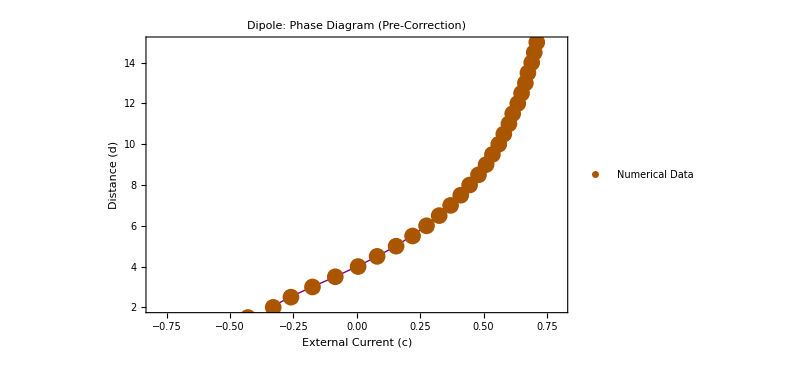
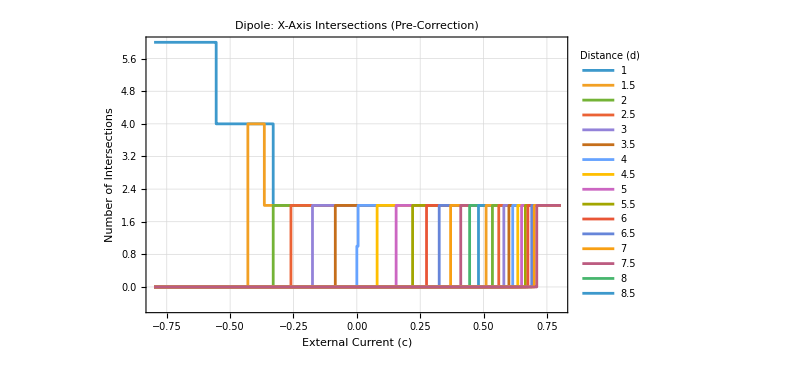
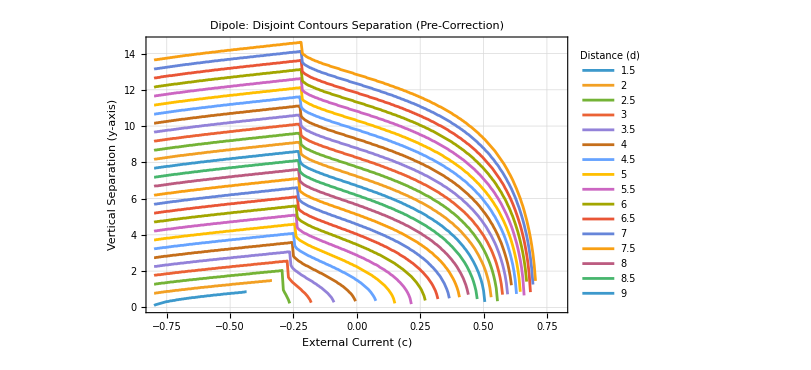
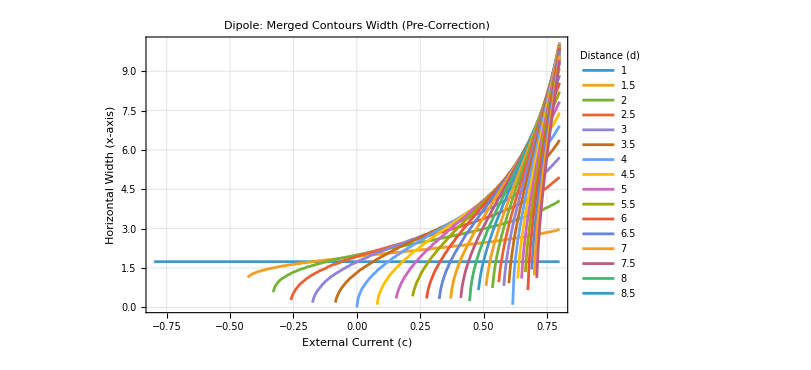
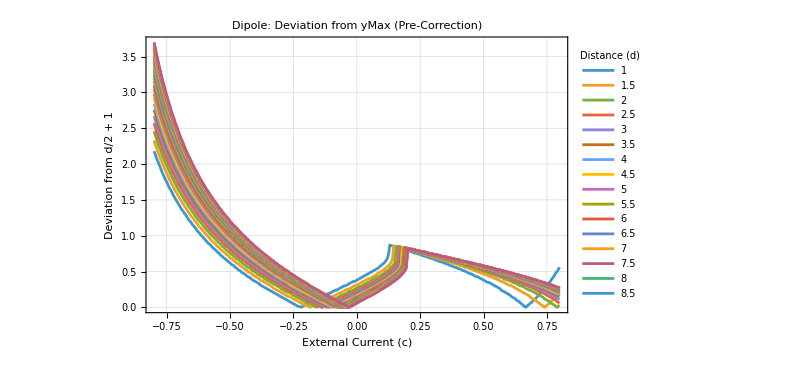
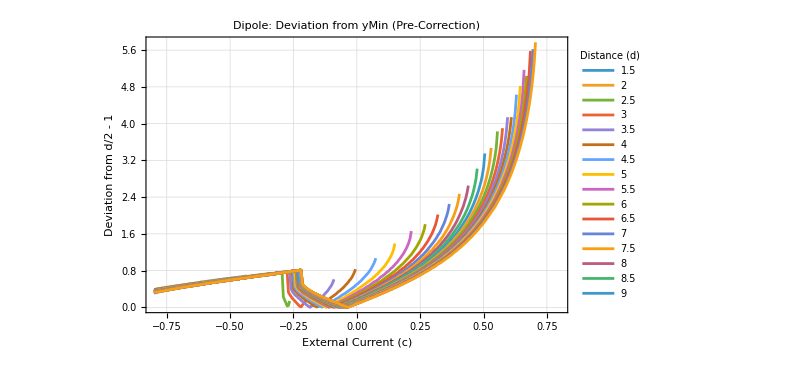
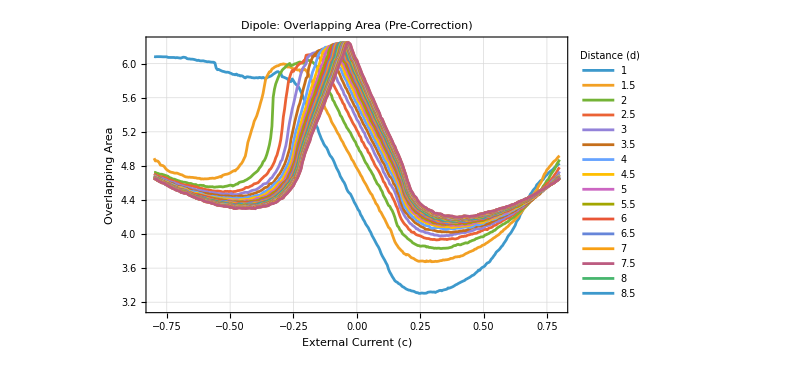
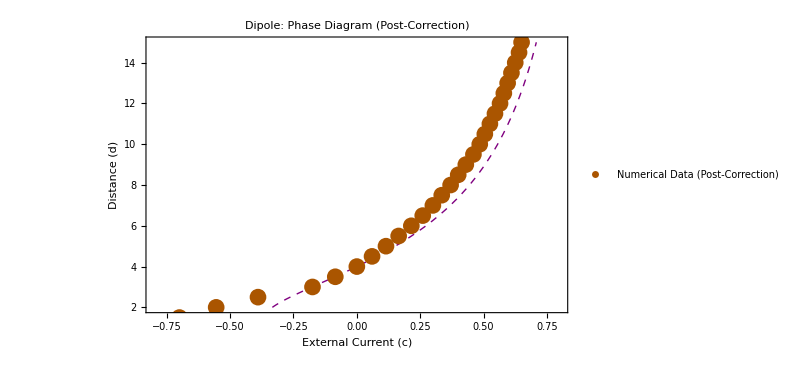
```mathematica
(*Estrazione Dati Sistema Base (Pre-Correction)*)
dBaseCount3=Select[Table[{valoriD[[i]],DeleteCases[datiBase3[[i,All,{1,2}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseY3=Select[Table[{valoriD[[i]],DeleteCases[datiBase3[[i,All,{1,3}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseX3=Select[Table[{valoriD[[i]],DeleteCases[datiBase3[[i,All,{1,4}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseTopMax3=Select[Table[{valoriD[[i]],DeleteCases[datiBase3[[i,All,{1,5}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseTopMin3=Select[Table[{valoriD[[i]],DeleteCases[datiBase3[[i,All,{1,6}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dBaseArea3=Select[Table[{valoriD[[i]],DeleteCases[datiBase3[[i,All,{1,7}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
puntiFaseBase3=DeleteCases[Table[Module[{cCrit},cCrit=SelectFirst[datiBase3[[i]],#[[2]]>=2&];If[MissingQ[cCrit],Missing[],{cCrit[[1]],valoriD[[i]]}]],{i,1,Length[valoriD]}],_Missing];

(*Estrazione Dati Sistema Feedback (Post-Correction)*)
dCorrCount3=Select[Table[{valoriD[[i]],DeleteCases[datiCorr3[[i,All,{1,2}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrY3=Select[Table[{valoriD[[i]],DeleteCases[datiCorr3[[i,All,{1,3}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrX3=Select[Table[{valoriD[[i]],DeleteCases[datiCorr3[[i,All,{1,4}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrTopMax3=Select[Table[{valoriD[[i]],DeleteCases[datiCorr3[[i,All,{1,5}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrTopMin3=Select[Table[{valoriD[[i]],DeleteCases[datiCorr3[[i,All,{1,6}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
dCorrArea3=Select[Table[{valoriD[[i]],DeleteCases[datiCorr3[[i,All,{1,7}]],{_,_Missing}]},{i,Length[valoriD]}],Length[#[[2]]]>0&];
puntiFaseCorr3=DeleteCases[Table[Module[{cCrit},cCrit=SelectFirst[datiCorr3[[i]],MissingQ[#[[2]]]||(NumericQ[#[[2]]]&&#[[2]]>=2)&];If[MissingQ[cCrit],Missing[],{cCrit[[1]],valoriD[[i]]}]],{i,1,Length[valoriD]}],_Missing];


(* =========================================================================*)
(*PARTE 2:SALVATAGGIO DEI DATI IN JSON PER PYTHON*)
(* =========================================================================*)
Print[Style["2. Esportazione dati in formato JSON...",14,Bold,Darker[Green]]];

datiEsportazione=<|"valoriD"->valoriD,"rangeC"->rangeC,"dBaseCount3"->dBaseCount3,"dBaseY3"->dBaseY3,"dBaseX3"->dBaseX3,"dBaseTopMax3"->dBaseTopMax3,"dBaseTopMin3"->dBaseTopMin3,"dBaseArea3"->dBaseArea3,"puntiFaseBase3"->puntiFaseBase3,"dCorrCount3"->dCorrCount3,"dCorrY3"->dCorrY3,"dCorrX3"->dCorrX3,"dCorrTopMax3"->dCorrTopMax3,"dCorrTopMin3"->dCorrTopMin3,"dCorrArea3"->dCorrArea3,"puntiFaseCorr3"->puntiFaseCorr3|>;

percorsoJSON=FileNameJoin[{cartellaExport,"DatiDipoloUnificati3.json"}];
Export[percorsoJSON,datiEsportazione,"JSON"];
Print["Dati esportati con successo in: ",percorsoJSON];

"1. Avvio Calcolo Massivo Unificato Feedback (yMin+1)..."
"(Il calcolo numerico delle aree richiederà un po' più di tempo)"
"2. Esportazione dati in formato JSON..."
"Dati esportati con successo in: ""C:\\Users\\franc\\OneDrive\\Documenti\\Wolfram\\DatiDipoloUnificati3.json"
(* =========================================================================*)
(*PARTE 3:GENERAZIONE GRAFICI E SIMULATORE*)
(* =========================================================================*)
Print[Style["3. Creazione Grafici e Interfacce...",14,Bold,Darker[Purple]]];

(*Opzioni Estetiche*)
opzioniComuni={Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],PlotStyle->AbsoluteThickness[2],PlotMarkers->None,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],PlotRange->{{-0.8,0.8},All},ImageSize->600};
opzioniConteggio3=Append[FilterRules[opzioniComuni,Except[PlotRange]],PlotRange->{{-0.8,0.8},{-0.5,6}}];
curvaFaseEsatta3[d_]:=(d^2-4 d)/(d^2+8);

(*---Simulatore Interattivo---*)
simulatore=Manipulate[ContourPlot[Evaluate[velSq[x,y,c,d]==1],{x,-5,5},{y,-5,5},PlotPoints->60,MaxRecursion->2,FrameLabel->{"Re(z) = x","Im(z) = y"},PlotLabel->Style["Critical Velocity Contour: |v| = 1",Bold,14],ContourStyle->Directive[Thick,Blue],PlotTheme->"Detailed",Epilog->{Directive[Thick,Red],Circle[{0,d/2},1],Circle[{0,-d/2},1]}],{{c,0.1,"External Current (c)"},0,0.5,Appearance->"Labeled"},{{d,6,"Distance Parameter (d)"},2,15,Appearance->"Labeled"},ContinuousAction->False,SaveDefinitions->True];

(*---Grafici Fase---*)
plotFaseBase3=Show[ParametricPlot[{curvaFaseEsatta3[d],d},{d,2,15},PlotStyle->Directive[Thick,Purple]],ListPlot[puntiFaseBase3,PlotStyle->Directive[PointSize[0.02],Darker[Orange]],PlotLegends->Placed[PointLegend[{Style["Numerical Data",11]},LegendMarkers->Automatic],{0.8,0.2}]],PlotRange->{{-0.8,0.8},{2,15}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],AspectRatio->1/GoldenRatio,ImageSize->600,FrameLabel->{Style["External Current (c)",12,Bold],Style["Distance (d)",12,Bold]},PlotLabel->Style["Dipole: Phase Diagram (Pre-Correction)",14,Bold,Darker[Purple]]];

plotFaseCorr3=Show[ParametricPlot[{curvaFaseEsatta3[d],d},{d,2,15},PlotStyle->Directive[Thick,Purple,Dashed]],ListPlot[puntiFaseCorr3,PlotStyle->Directive[PointSize[0.02],Darker[Orange]],PlotLegends->Placed[PointLegend[{Style["Numerical Data (Post-Correction)",11]},LegendMarkers->Automatic],{0.8,0.2}]],PlotRange->{{-0.8,0.8},{2,15}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],AspectRatio->1/GoldenRatio,ImageSize->600,FrameLabel->{Style["External Current (c)",12,Bold],Style["Distance (d)",12,Bold]},PlotLabel->Style["Dipole: Phase Diagram (Post-Correction)",14,Bold,Darker[Purple]]];

(*---Grafici Base (Pre-Correction)---*)
pCountXBase3=ListStepPlot[dBaseCount3[[All,2]],Sequence@@opzioniConteggio3,PlotLegends->Placed[PointLegend[dBaseCount3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Number of Intersections",12]},PlotLabel->Style["Dipole: X-Axis Intersections (Pre-Correction)",14,Bold,Darker[Orange]]];
pDistanzaLobiBase3=ListLinePlot[dBaseY3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseY3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Vertical Separation (y-axis)",12]},PlotLabel->Style["Dipole: Disjoint Contours Separation (Pre-Correction)",14,Bold,Darker[Red]]];
pDistanzaXBase3=ListLinePlot[dBaseX3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseX3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Horizontal Width (x-axis)",12]},PlotLabel->Style["Dipole: Merged Contours Width (Pre-Correction)",14,Bold,Darker[Blue]]];
pDistTopMaxBase3=ListLinePlot[dBaseTopMax3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseTopMax3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Deviation from d/2 + 1",12]},PlotLabel->Style["Dipole: Deviation from yMax (Pre-Correction)",14,Bold,Darker[Green]]];
pDistTopMinBase3=ListLinePlot[dBaseTopMin3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseTopMin3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Deviation from d/2 - 1",12]},PlotLabel->Style["Dipole: Deviation from yMin (Pre-Correction)",14,Bold,Darker[Magenta]]];
pAreaBase3=ListLinePlot[dBaseArea3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dBaseArea3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Overlapping Area",12]},PlotLabel->Style["Dipole: Overlapping Area (Pre-Correction)",14,Bold,Darker[Purple]]];

(*---Grafici Feedback (Post-Correction)---*)
pCountXCorr3=ListStepPlot[dCorrCount3[[All,2]],Sequence@@opzioniConteggio3,PlotLegends->Placed[PointLegend[dCorrCount3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Number of Intersections",12]},PlotLabel->Style["Dipole: X-Axis Intersections (Post-Correction)",14,Bold,Darker[Orange]]];
pDistanzaLobiCorr3=ListLinePlot[dCorrY3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrY3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Vertical Separation (y-axis)",12]},PlotLabel->Style["Dipole: Disjoint Contours Separation (Post-Correction)",14,Bold,Darker[Red]]];
pDistanzaXCorr3=ListLinePlot[dCorrX3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrX3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Horizontal Width (x-axis)",12]},PlotLabel->Style["Dipole: Merged Contours Width (Post-Correction)",14,Bold,Darker[Blue]]];
pDistTopMaxCorr3=ListLinePlot[dCorrTopMax3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrTopMax3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Deviation from dNew/2 + 1",12]},PlotLabel->Style["Dipole: Deviation from yMax (Post-Correction)",14,Bold,Darker[Green]]];
pDistTopMinCorr3=ListLinePlot[dCorrTopMin3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrTopMin3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Deviation from dNew/2 - 1",12]},PlotLabel->Style["Dipole: Deviation from yMin (Post-Correction)",14,Bold,Darker[Magenta]]];
pAreaCorr3=ListLinePlot[dCorrArea3[[All,2]],Sequence@@opzioniComuni,PlotLegends->Placed[PointLegend[dCorrArea3[[All,1]],LegendLabel->Style["Distance (d)",12,Bold],LegendLayout->{"Row",3}],Below],FrameLabel->{Style["External Current (c)",12],Style["Overlapping Area",12]},PlotLabel->Style["Dipole: Overlapping Area (Post-Correction)",14,Bold,Darker[Purple]]];

(*---Stampa a Video Finale---*)
Print[simulatore];

Print[Style["\n--- RISULTATI SISTEMA BASE (PRE-CORRECTION) ---",16,Bold,Darker[Green]]];
Print[plotFaseBase3];
Print[pCountXBase3];Print[pDistanzaLobiBase3];Print[pDistanzaXBase3];Print[pDistTopMaxBase3];Print[pDistTopMinBase3];Print[pAreaBase3];

Print[Style["\n--- RISULTATI FEEDBACK (POST-CORRECTION: dNew = 2*(yMin+1)) ---",16,Bold,Darker[Cyan]]];
Print[plotFaseCorr3];
Print[pCountXCorr3];Print[pDistanzaLobiCorr3];Print[pDistanzaXCorr3];Print[pDistTopMaxCorr3];Print[pDistTopMinCorr3];Print[pAreaCorr3];
"3. Creazione Grafici e Interfacce..."

"\n--- RISULTATI SISTEMA BASE (PRE-CORRECTION) ---"
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
"\n--- RISULTATI FEEDBACK (POST-CORRECTION: dNew = 2*(yMin+1)) ---"
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
```

### Caso con Linee Separate

```mathematica
Clear[c,cval,d,y];
cval= 0;
d=8;

(*1. Inizializza la fisica (c viene trattato come parametro simbolico)*)
ImpostaFisica[I*c*(z+1/(z-I*d/2)+1/(z+I*d/2))+Log[z-I*d/2]-Log[z+I*d/2]];

(*Stampa i grafici usando la tua macro originale*)
StampaGrafici[ostacoloDoppio,"=== CASO CON LINEE SEPARATE (Senza Correzione) ===",d,"C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","linsep_nocorr",cval];

(* =========================================================================*)(*2. Calcoliamo TUTTE le soluzioni per y (con x=0)*)(* =========================================================================*)(*Usa la regola di sostituzione (/. c->cval) invece di assegnare c=cval*)(*Questo mantiene'c' come simbolo globale intatto per cicli futuri*)soluzioni=y/. Quiet[NSolve[(vel[0,y]/. c->cval)==1&&-30<=y<=30,y,Reals]];

(*Protezione nel caso NSolve non trovi soluzioni reali*)
If[!ListQ[soluzioni],soluzioni={}];

soluzioni=Flatten[{soluzioni}];
soluzioni=Re[Select[soluzioni,NumericQ]];

(*Controllo validità usando la sostituzione*)
soluzioni=Select[soluzioni,Abs[(vel[0,#]/. c->cval)-1]<0.001&];
soluzioni=Sort[N[DeleteDuplicates[Round[soluzioni,0.0001]]]];

(*3. Filtriamo SOLO le soluzioni strettamente positive (y>0)*)
solPositive=Select[soluzioni,#>0&];

(*4. Calcoli e Stampe*)
If[Length[solPositive]>=2,Module[{bordoSup,bordoInf},yMax=Max[solPositive];
yMin=Min[solPositive];
bordoSup=d/2+1;
bordoInf=d/2-1;
(*Variabili globali per dist1 e dist2 mantenute*)dist1=Abs[bordoSup-yMax];
dist2=Abs[bordoInf-yMin];
Print[Style["\n=== RISULTATI ANALISI (c="<>ToString[cval]<>", d="<>ToString[d]<>") ===",14,Bold,Darker[Blue]]];
Print[Style["Soluzioni positive valide per y: "<>ToString[solPositive],12]];
Print[""];
(*Correzione:usiamo le variabili al posto dei numeri hard-coded*)Print[Style["Distanza (Bordo Superiore - yMax):",12,Bold]," |",bordoSup," - ",yMax,"| = ",Style[dist1,14,Darker[Green],Bold]];
Print[Style["Distanza (Bordo Inferiore - yMin):",12,Bold]," |",bordoInf," - ",yMin,"| = ",Style[dist2,14,Darker[Red],Bold]];],Print[Style["\nAttenzione: Trovate meno di 2 soluzioni positive: "<>ToString[solPositive],12,Red]]]
```

### Caso con Linee Separate (con Correzione Media)

```mathematica
(* =========================================================================*)(*CASO CON CORREZIONE DELLA DISTANZA (dcorrect)*)(* =========================================================================*)dcorrect=(yMax+yMin+d)/2; (*Uso la media tra la distanza di prima e la nuova corretta*)

ostacoloDoppio={FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,-dcorrect/2},1],AbsoluteThickness[1.5],Green,Circle[{0,-dcorrect/2},1],FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,+dcorrect/2},1],AbsoluteThickness[1.5],Green,Circle[{0,dcorrect/2},1]};

(*1. Inizializza la fisica (c viene trattato come parametro simbolico)*)
ImpostaFisica[I*c*(z+1/(z-I*dcorrect/2)+1/(z+I*dcorrect/2))+Log[z-I*d/2]-Log[z+I*d/2]];

StampaGrafici[ostacoloDoppio,"=== CASO CON LINEE SEPARATE (Con Correzione) ===",dcorrect,"C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","linsep_corrmed",cval];

(* =========================================================================
(*2. Calcoliamo TUTTE le soluzioni per y (con x=0)*)
(* =========================================================================*)

c=cval; (*Assegniamo il valore a c per la valutazione numerica*)

soluzioni=y/. Quiet[NSolve[vel[0,y]==1&&-30<=y<=30,y,Reals]];

(*Protezione nel caso NSolve fallisca o non trovi soluzioni*)
If[!ListQ[soluzioni],soluzioni={}];

soluzioni=Flatten[{soluzioni}];
soluzioni=Re[Select[soluzioni,NumericQ]];
soluzioni=Select[soluzioni,Abs[(vel[0,#])-1]<0.001&];
soluzioni=Sort[N[DeleteDuplicates[Round[soluzioni,0.0001]]]];

(*3. Filtriamo SOLO le soluzioni strettamente positive (y>0)*)
solPositive=Select[soluzioni,#>0&];

(*4. Calcoli e Stampe*)
If[Length[solPositive]>=2,Module[{bordoSup,bordoInf},yMax1=Max[solPositive];
yMin1=Min[solPositive];
bordoSup=dcorrect/2+1;
bordoInf=dcorrect/2-1;
(*Variabili globali per dist1 e dist2 mantenute*)dist1=Abs[bordoSup-yMax1];
dist2=Abs[bordoInf-yMin1];
Print[Style["\n=== RISULTATI ANALISI (c="<>ToString[cval]<>", dcorrect="<>ToString[dcorrect]<>") ===",14,Bold,Darker[Blue]]];
Print[Style["Soluzioni positive valide per y: "<>ToString[solPositive],12]];
Print[""];
(*Le stringhe ora stampano i bordi calcolati dinamicamente*)Print[Style["Distanza (Bordo Superiore - yMax):",12,Bold]," |",bordoSup," - ",yMax1,"| = ",Style[dist1,14,Darker[Green],Bold]];
Print[Style["Distanza (Bordo Inferiore - yMin):",12,Bold]," |",bordoInf," - ",yMin1,"| = ",Style[dist2,14,Darker[Red],Bold]];],Print[Style["\nAttenzione: Trovate meno di 2 soluzioni positive: "<>ToString[solPositive],12,Red]]]*)
```

### Caso con Linee Separate (con Correzione Forte)

```mathematica
(* =========================================================================*)(*CASO CON CORREZIONE DELLA DISTANZA (dcorrect=yMax+yMin)*)(* =========================================================================*)
dcorrect=yMax+yMin; (*Uso la somma diretta delle posizioni precedenti*)

ostacoloDoppio={FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,-dcorrect/2},1],AbsoluteThickness[1.5],Green,Circle[{0,-dcorrect/2},1],FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,+dcorrect/2},1],AbsoluteThickness[1.5],Green,Circle[{0,dcorrect/2},1]};

(*1. Inizializza la fisica (c viene trattato come parametro simbolico)*)
ImpostaFisica[I*c*(z+1/(z-I*dcorrect/2)+1/(z+I*dcorrect/2))+Log[z-I*d/2]-Log[z+I*d/2]];

StampaGrafici[ostacoloDoppio,"=== CASO CON LINEE SEPARATE (Con Correzione Forte) ===",dcorrect,"C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","linsep_corrfor",cval];

(* =========================================================================
(*2. Calcoliamo TUTTE le soluzioni per y (con x=0)*)
(* =========================================================================*)

c=cval; (*Assegniamo il valore a c per la valutazione numerica*)

soluzioni=y/. Quiet[NSolve[vel[0,y]==1&&-30<=y<=30,y,Reals]];

(*Protezione nel caso NSolve fallisca o non trovi soluzioni*)
If[!ListQ[soluzioni],soluzioni={}];

soluzioni=Flatten[{soluzioni}];
soluzioni=Re[Select[soluzioni,NumericQ]];
soluzioni=Select[soluzioni,Abs[(vel[0,#])-1]<0.001&];
soluzioni=Sort[N[DeleteDuplicates[Round[soluzioni,0.0001]]]];

(*3. Filtriamo SOLO le soluzioni strettamente positive (y>0)*)
solPositive=Select[soluzioni,#>0&];

(*4. Calcoli e Stampe*)
If[Length[solPositive]>=2,Module[{bordoSup,bordoInf},yMax=Max[solPositive];
yMin=Min[solPositive];
bordoSup=dcorrect/2+1;
bordoInf=dcorrect/2-1;
(*Variabili globali per dist1 e dist2 mantenute*)dist1=Abs[bordoSup-yMax];
dist2=Abs[bordoInf-yMin];
Print[Style["\n=== RISULTATI ANALISI (c="<>ToString[cval]<>", dcorrect="<>ToString[dcorrect]<>") ===",14,Bold,Darker[Blue]]];
Print[Style["Soluzioni positive valide per y: "<>ToString[solPositive],12]];
Print[""];
(*Le stringhe ora stampano i bordi calcolati dinamicamente basati sul nuovo dcorrect*)Print[Style["Distanza (Bordo Superiore - yMax):",12,Bold]," |",bordoSup," - ",yMax,"| = ",Style[dist1,14,Darker[Green],Bold]];
Print[Style["Distanza (Bordo Inferiore - yMin):",12,Bold]," |",bordoInf," - ",yMin,"| = ",Style[dist2,14,Darker[Red],Bold]];],Print[Style["\nAttenzione: Trovate meno di 2 soluzioni positive: "<>ToString[solPositive],12,Red]]]*)
```

### Caso con circonferenza poggiata sul minimo

```mathematica
(* =========================================================================*)(*CASO CON CORREZIONE DELLA DISTANZA (dcorrect=yMin+1)*)(* =========================================================================*)dcorrect=2*(yMin+1); (*Nuovo criterio di feedback basato sul limite inferiore*)

ostacoloDoppio={FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,-dcorrect/2},1],AbsoluteThickness[1.5],Green,Circle[{0,-dcorrect/2},1],FaceForm[Directive[White,Opacity[0.5]]],Disk[{0,+dcorrect/2},1],AbsoluteThickness[1.5],Green,Circle[{0,dcorrect/2},1]};

(*1. Inizializza la fisica (c viene trattato come parametro simbolico)*)
ImpostaFisica[I*c*(z+1/(z-I*dcorrect/2)+1/(z+I*dcorrect/2))+Log[z-I*d/2]-Log[z+I*d/2]];

StampaGrafici[ostacoloDoppio,"=== CASO CON LINEE SEPARATE (Correzione yMin + 1) ===",dcorrect,"C:\\Users\\franc\\OneDrive\\Documenti\\Università\\Tesi\\Wolfram","linsep_corrymin1",cval];

(* =========================================================================
(*2. Calcoliamo TUTTE le soluzioni per y (con x=0)*)
(* =========================================================================*)

c=cval; (*Assegniamo il valore a c per la valutazione numerica*)

soluzioni=y/. Quiet[NSolve[vel[0,y]==1&&-30<=y<=30,y,Reals]];

(*Protezione nel caso NSolve fallisca o non trovi soluzioni*)
If[!ListQ[soluzioni],soluzioni={}];

soluzioni=Flatten[{soluzioni}];
soluzioni=Re[Select[soluzioni,NumericQ]];
soluzioni=Select[soluzioni,Abs[(vel[0,#])-1]<0.001&];
soluzioni=Sort[N[DeleteDuplicates[Round[soluzioni,0.0001]]]];

(*3. Filtriamo SOLO le soluzioni strettamente positive (y>0)*)
solPositive=Select[soluzioni,#>0&];

(*4. Calcoli e Stampe*)
If[Length[solPositive]>=2,Module[{bordoSup,bordoInf},yMax=Max[solPositive];
yMin=Min[solPositive];
bordoSup=dcorrect/2+1;
bordoInf=dcorrect/2-1;
(*Variabili globali per dist1 e dist2 mantenute*)dist1=Abs[bordoSup-yMax];
dist2=Abs[bordoInf-yMin];
Print[Style["\n=== RISULTATI ANALISI (c="<>ToString[cval]<>", dcorrect="<>ToString[dcorrect]<>") ===",14,Bold,Darker[Blue]]];
Print[Style["Soluzioni positive valide per y: "<>ToString[solPositive],12]];
Print[""];
(*Le stringhe ora stampano i bordi calcolati dinamicamente basati sul nuovo dcorrect*)Print[Style["Distanza (Bordo Superiore - yMax):",12,Bold]," |",bordoSup," - ",yMax,"| = ",Style[dist1,14,Darker[Green],Bold]];
Print[Style["Distanza (Bordo Inferiore - yMin):",12,Bold]," |",bordoInf," - ",yMin,"| = ",Style[dist2,14,Darker[Red],Bold]];],Print[Style["\nAttenzione: Trovate meno di 2 soluzioni positive: "<>ToString[solPositive],12,Red]]]*)
```

```mathematica
q
```